```mathematica
ClearAll["Global`*"]
```

### Pion Distribution

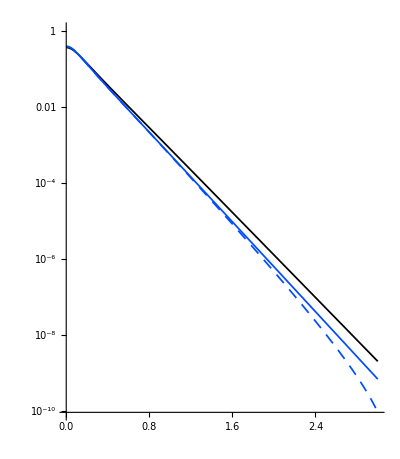

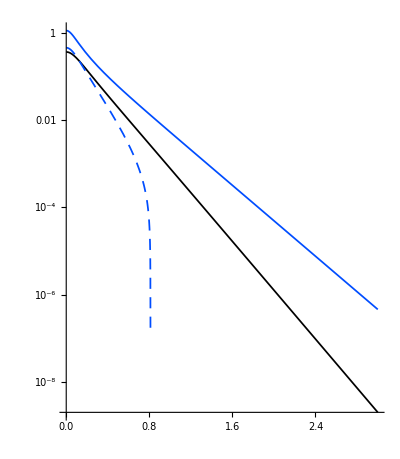

```mathematica
hbarC = 0.197327053;
prefactor = 1.0/(2.0*Pi*hbarC)^3;
T = 0.155024;                                 (* temperature in GeV *)
P = 0.269886 * hbarC;  (* equilibrium pressure in GeV / fm^3*)
F = -0.0234907;
betaPi=0.0195753;                   (* betaPi in GeV / fm^3*)
mpion = 0.13957;                         (* pion mass in GeV *)
(*equilibrium*)
feqpion[p_]=(1.0*prefactor)/(Exp[Sqrt[mpion^2+p^2]/T]-1);
(* Modified distribution: Π = -0.1 * P *)
Π1 =-0.1 * P; 
dT1 = 0.0063908;
Zpion1 = 1.00678;
M1 = 1.0 + Π1/(3.0*betaPi );
fmodpion1[p_]=(Zpion1*prefactor)/(Exp[Sqrt[mpion^2+(p/M1)^2]/(T+dT1)]-1);
fCEpion1[p_]=feqpion[p] + feqpion[p]*(1+feqpion[p]/prefactor)*((Sqrt[mpion^2+p^2]*F)/T^2+p^2/(3.0*T*Sqrt[mpion^2+p^2]))*Π1/betaPi;
(* Modified distribution: Π = -0.4 * P *)
Π2 =-0.4 * P; 
dT2 = 0.180588;
Zpion2 = 1.09039;
M2= 1.0 + Π2/(3.0*betaPi );
fmodpion2[p_]=(Zpion2*prefactor)/(Exp[Sqrt[mpion^2+(p/M2)^2]/(T+dT2)]-1);
fCEpion2[p_]=feqpion[p] + feqpion[p]*(1+feqpion[p]/prefactor)*((Sqrt[mpion^2+p^2]*F)/T^2+p^2/(3.0*T*Sqrt[mpion^2+p^2]))*Π2/betaPi;
blue = RGBColor[0,0.3,1];
LogPlot[{feqpion[p],fCEpion1[p],fmodpion1[p]},{p,0.,3},PlotStyle->{Directive[Black,AbsoluteThickness[1.25]],
Directive[blue,AbsoluteThickness[1.25],AbsoluteDashing[{8,6}]],Directive[blue,AbsoluteThickness[1.25]]},ImageSize->400,AspectRatio->1.15]
LogPlot[{feqpion[p],fCEpion2[p],fmodpion2[p]},{p,0.,3},PlotStyle->{Directive[Black,AbsoluteThickness[1.25]],
Directive[blue,AbsoluteThickness[1.25],AbsoluteDashing[{8,6}]],Directive[blue,AbsoluteThickness[1.25]]},ImageSize->400,AspectRatio->1.15]
```

### Kaon Distribution

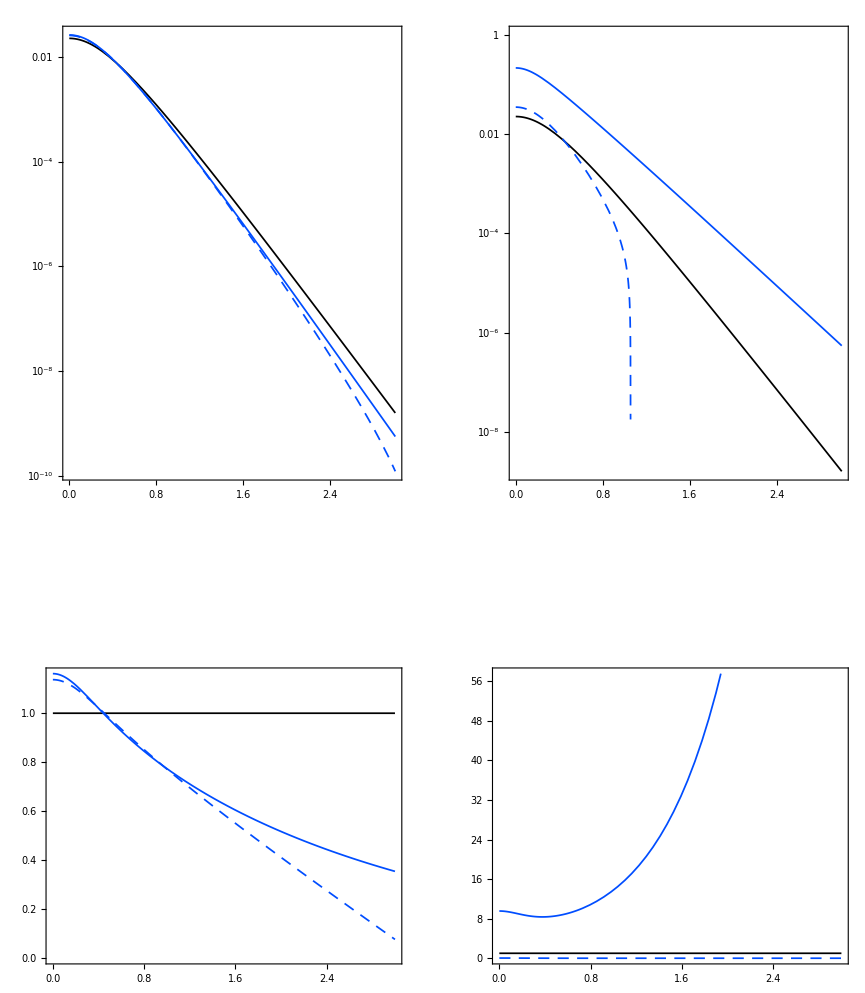

```mathematica
hbarC = 0.197327053;
prefactor = 1.0/(2.0*Pi*hbarC)^3;
T = 0.155024;                                 (* temperature in GeV *)
P = 0.269886 * hbarC;  (* equilibrium pressure in GeV / fm^3*)
betaPi=0.0195753;                   (* betaPi in GeV / fm^3*)
mkaon = 0.49368;                         (* pion mass in GeV *)
(*equilibrium*)
feqkaon[p_]=(1.0*prefactor)/(Exp[Sqrt[mkaon^2+p^2]/T]-1);
(* Modified distribution: Π = -0.1 * P *)
Π1 =-0.1 * P; 
dT1 = 0.0063908;
Zkaon1 = 1.01797;
M1 = 1.0 + Π1/(3.0*betaPi );
fmodkaon1[p_]=(Zkaon1*prefactor)/(Exp[Sqrt[mkaon^2+(p/M1)^2]/(T+dT1)]-1);
fCEkaon1[p_]=feqkaon[p] + feqkaon[p]*(1+feqkaon[p]/prefactor)*((Sqrt[mkaon^2+p^2]*F)/T^2+p^2/(3.0*T*Sqrt[mkaon^2+p^2]))*Π1/betaPi;
(* Modified distribution: Π = -0.4 * P *)
Π2 =-0.4 * P; 
dT2 = 0.180588;
Zkaon2 = 1.38231;
M2= 1.0 + Π2/(3.0*betaPi );
fmodkaon2[p_]=(Zkaon2*prefactor)/(Exp[Sqrt[mkaon^2+(p/M2)^2]/(T+dT2)]-1);
fCEkaon2[p_]=feqkaon[p] + feqkaon[p]*(1+feqkaon[p]/prefactor)*((Sqrt[mkaon^2+p^2]*F)/T^2+p^2/(3.0*T*Sqrt[mkaon^2+p^2]))*Π2/betaPi;
blue = RGBColor[0,0.3,1];

GraphicsGrid[{{LogPlot[{feqkaon[p],fCEkaon1[p],fmodkaon1[p]},{p,0,3},Frame->True,PlotStyle->{Directive[Black,AbsoluteThickness[1.25]],
Directive[blue,AbsoluteThickness[1.25],AbsoluteDashing[{8,6}]],Directive[blue,AbsoluteThickness[1.25]]},ImageSize->400,AspectRatio->1.15],LogPlot[{feqkaon[p],fCEkaon2[p],fmodkaon2[p]},{p,0,3},Frame->True,PlotStyle->{Directive[Black,AbsoluteThickness[1.25]],
Directive[blue,AbsoluteThickness[1.25],AbsoluteDashing[{8,6}]],Directive[blue,AbsoluteThickness[1.25]]},ImageSize->400,AspectRatio->1.15]
},
{Plot[{1.0,fCEkaon1[p]/feqkaon[p],fmodkaon1[p]/feqkaon[p]},{p,0,3},Frame->True,PlotStyle->{Directive[Black,AbsoluteThickness[1.25]],
Directive[blue,AbsoluteThickness[1.25],AbsoluteDashing[{8,6}]],Directive[blue,AbsoluteThickness[1.25]]},ImageSize->400,AspectRatio->0.75],Plot[{1.0,fCEkaon2[p],fmodkaon2[p]/feqkaon[p]},{p,0,3},Frame->True,PlotStyle->{Directive[Black,AbsoluteThickness[1.25]],
Directive[blue,AbsoluteThickness[1.25],AbsoluteDashing[{8,6}]],Directive[blue,AbsoluteThickness[1.25]]},ImageSize->400,AspectRatio->0.75]}}]
```

### Proton Distribution

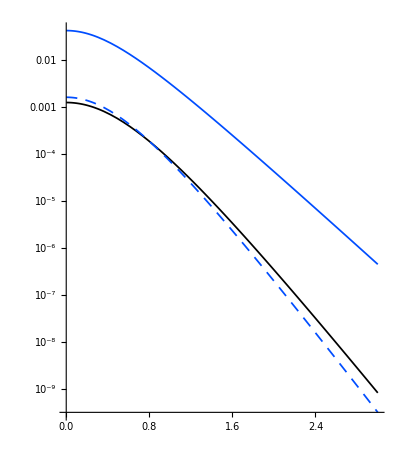

```mathematica
hbarC = 0.197327053;
prefactor = 1.0/(2.0*Pi*hbarC)^3;
T = 0.155024;                                 (* temperature in GeV *)
P = 0.269886 * hbarC;  (* equilibrium pressure in GeV / fm^3*)
betaPi=0.0195753;                   (* betaPi in GeV / fm^3*)
mproton = 0.93827;                         (* pion mass in GeV *)
(*equilibrium*)
feqproton[p_]=(1.0*prefactor)/(Exp[Sqrt[mproton^2+p^2]/T]+1);
(* Modified distribution: Π = -0.1 * P *)
Π1 =-0.1 * P; 
dT1 = 0.0063908;
Zproton1 = 1.01797;
M1 = 1.0 + Π1/(3.0*betaPi );
fmodproton1[p_]=(Zproton1*prefactor)/(Exp[Sqrt[mproton^2+(p/M1)^2]/(T+dT1)]+1);
(* Modified distribution: Π = -0.4 * P *)
Π2 =-0.4 * P; 
dT2 = 0.180588;
Zproton2 = 1.38231;
M2= 1.0 + Π2/(3.0*betaPi );
fmodproton2[p_]=(Zproton2*prefactor)/(Exp[Sqrt[mproton^2+(p/M2)^2]/(T+dT2)]+1);
blue = RGBColor[0,0.3,1];
LogPlot[{feqproton[p],fmodproton1[p],fmodproton2[p]},{p,0,3},PlotStyle->{Directive[Black,AbsoluteThickness[1.25]],
Directive[blue,AbsoluteThickness[1.25],AbsoluteDashing[{8,6}]],Directive[blue,AbsoluteThickness[1.25]]},ImageSize->400,AspectRatio->1.15]
```

### Pion

```mathematica
idealπ=
{{7.17752430*10^-03,2.01939637*10^+02},{3.78993630*10^-02,2.02051375*10^+02},{9.35073360*10^-02,1.98657813*10^+02},{1.74611500*10^-01,1.77252617*10^+02},{2.82124830*10^-01,1.35205960*10^+02},{4.17333600*10^-01,8.95559489*10^+01},{5.81993540*10^-01,5.30861632*10^+01},{7.78479140*10^-01,2.86070980*10^+01},{1.01002170*10^+00,1.40323350*10^+01},{1.28110830*10^+00,6.20952680*10^+00},{1.59819070*10^+00,2.43629368*10^+00},{1.97106870*10^+00,8.24511217*10^-01},{2.41596300*10^+00,2.30044631*10^-01},{2.96389860*10^+00,4.85663778*10^-02}};


shear14π={{7.17752430*10^-03,2.02445071*10^+02},{3.78993630*10^-02,2.02377534*10^+02},{9.35073360*10^-02,1.98289128*10^+02},{1.74611500*10^-01,1.76000649*10^+02},{2.82124830*10^-01,1.33634031*10^+02},{4.17333600*10^-01,8.82585568*10^+01},{5.81993540*10^-01,5.22870918*10^+01},{7.78479140*10^-01,2.82665140*10^+01},{1.01002170*10^+00,1.39995020*10^+01},{1.28110830*10^+00,6.31953648*10^+00},{1.59819070*10^+00,2.56818609*10^+00},{1.97106870*10^+00,9.19878476*10^-01},{2.41596300*10^+00,2.79799342*10^-01},{2.96389860*10^+00,6.71023520*10^-02}};

shearCEπ=
{{7.17752430*10^-03,2.04618817*10^+02},{3.78993630*10^-02,2.03709717*10^+02},{9.35073360*10^-02,1.96683595*10^+02},{1.74611500*10^-01,1.71844882*10^+02},{2.82124830*10^-01,1.29954179*10^+02},{4.17333600*10^-01,8.63335201*10^+01},{5.81993540*10^-01,5.17501190*10^+01},{7.78479140*10^-01,2.84258383*10^+01},{1.01002170*10^+00,1.43445251*10^+01},{1.28110830*10^+00,6.59918977*10^+00},{1.59819070*10^+00,2.72277175*10^+00},{1.97106870*10^+00,9.80927868*10^-01},{2.41596300*10^+00,2.95256790*10^-01},{2.96389860*10^+00,6.83362003*10^-02}};

shearmodπ ={{7.17752430*10^-03,2.04620236*10^+02},{3.78993630*10^-02,2.03981201*10^+02},{9.35073360*10^-02,1.97787507*10^+02},{1.74611500*10^-01,1.73266292*10^+02},{2.82124830*10^-01,1.30625292*10^+02},{4.17333600*10^-01,8.61800001*10^+01},{5.81993540*10^-01,5.11970737*10^+01},{7.78479140*10^-01,2.78299730*10^+01},{1.01002170*10^+00,1.38837625*10^+01},{1.28110830*10^+00,6.31389923*10^+00},{1.59819070*10^+00,2.57918871*10^+00},{1.97106870*10^+00,9.23756477*10^-01},{2.41596300*10^+00,2.78629357*10^-01},{2.96389860*10^+00,6.55571012*10^-02}};


bulk14π = {{7.17752430*10^-03,1.90663757*10^+02},{3.78993630*10^-02,1.90801591*10^+02},{9.35073360*10^-02,1.87244966*10^+02},{1.74611500*10^-01,1.64666848*10^+02},{2.82124830*10^-01,1.21028378*10^+02},{4.17333600*10^-01,7.52137106*10^+01},{5.81993540*10^-01,4.05033741*10^+01},{7.78479140*10^-01,1.88969500*10^+01},{1.01002170*10^+00,7.34873516*10^+00},{1.28110830*10^+00,2.10367891*10^+00},{1.59819070*10^+00,2.11287661*10^-01},{1.97106870*10^+00,-2.14615700*10^-01},{2.41596300*10^+00,-1.71729067*10^-01},{2.96389860*10^+00,-7.05821422*10^-02}};

bulkCEπ=
{{7.17752430*10^-03,1.77283821*10^+02},{3.78993630*10^-02,1.77624273*10^+02},{9.35073360*10^-02,1.73440953*10^+02},{1.74611500*10^-01,1.45851047*10^+02},{2.82124830*10^-01,9.77398374*10^+01},{4.17333600*10^-01,5.40536937*10^+01},{5.81993540*10^-01,2.54474196*10^+01},{7.78479140*10^-01,9.98184194*10^+00},{1.01002170*10^+00,2.89646926*10^+00},{1.28110830*10^+00,2.84465526*10^-01},{1.59819070*10^+00,-3.37713798*10^-01},{1.97106870*10^+00,-2.91367642*10^-01},{2.41596300*10^+00,-1.39843624*10^-01},{2.96389860*10^+00,-4.46592663*10^-02}};

bulkmodπ=
{{7.17752430*10^-03,1.62720175*10^+02},{3.78993630*10^-02,1.63038290*10^+02},{9.35073360*10^-02,1.58737994*10^+02},{1.74611500*10^-01,1.30552524*10^+02},{2.82124830*10^-01,8.48545002*10^+01},{4.17333600*10^-01,4.66730857*10^+01},{5.81993540*10^-01,2.27184465*10^+01},{7.78479140*10^-01,9.87132987*10^+00},{1.01002170*10^+00,3.79617023*10^+00},{1.28110830*10^+00,1.26952323*10^+00},{1.59819070*10^+00,3.59847784*10^-01},{1.97106870*10^+00,8.32472824*10^-02},{2.41596300*10^+00,1.47829113*10^-02},{2.96389860*10^+00,1.79361039*10^-03}};

shearbulk14π={{7.17752430*10^-03,1.91169190*10^+02},{3.78993630*10^-02,1.91127749*10^+02},{9.35073360*10^-02,1.86876281*10^+02},{1.74611500*10^-01,1.63414880*10^+02},{2.82124830*10^-01,1.19456448*10^+02},{4.17333600*10^-01,7.39163185*10^+01},{5.81993540*10^-01,3.97043027*10^+01},{7.78479140*10^-01,1.85563660*10^+01},{1.01002170*10^+00,7.31590211*10^+00},{1.28110830*10^+00,2.21368859*10^+00},{1.59819070*10^+00,3.43180073*10^-01},{1.97106870*10^+00,-1.19248441*10^-01},{2.41596300*10^+00,-1.21974356*10^-01},{2.96389860*10^+00,-5.20461680*10^-02}};

shearbulkCEπ={{7.17752430*10^-03,1.79963000*10^+02},{3.78993630*10^-02,1.79282614*10^+02},{9.35073360*10^-02,1.71466735*10^+02},{1.74611500*10^-01,1.40443313*10^+02},{2.82124830*10^-01,9.24880559*10^+01},{4.17333600*10^-01,5.08312650*10^+01},{5.81993540*10^-01,2.41113755*10^+01},{7.78479140*10^-01,9.80058224*10^+00},{1.01002170*10^+00,3.20865934*10^+00},{1.28110830*10^+00,6.74128495*10^-01},{1.59819070*10^+00,-5.12357307*10^-02},{1.97106870*10^+00,-1.34950992*10^-01},{2.41596300*10^+00,-7.46314658*10^-02},{2.96389860*10^+00,-2.48894438*10^-02}};

shearbulkmodπ={{7.17752430*10^-03,1.66511096*10^+02},{3.78993630*10^-02,1.65710031*10^+02},{9.35073360*10^-02,1.57196657*10^+02},{1.74611500*10^-01,1.25407351*10^+02},{2.82124830*10^-01,8.07966121*10^+01},{4.17333600*10^-01,4.47920748*10^+01},{5.81993540*10^-01,2.22718844*10^+01},{7.78479140*10^-01,1.00586660*10^+01},{1.01002170*10^+00,4.10620380*10^+00},{1.28110830*10^+00,1.49510448*10^+00},{1.59819070*10^+00,4.75813682*10^-01},{1.97106870*10^+00,1.28374101*10^-01},{2.41596300*10^+00,2.79361504*10^-02},{2.96389860*10^+00,4.45269816*10^-03}};

(*unregulated*)
shearbulkmodπ={{7.17752430*10^-03,1.67685417*10^+02},{3.78993630*10^-02,1.66761572*10^+02},{9.35073360*10^-02,1.57656327*10^+02},{1.74611500*10^-01,1.25178264*10^+02},{2.82124830*10^-01,8.02570949*10^+01},{4.17333600*10^-01,4.42759071*10^+01},{5.81993540*10^-01,2.19338727*10^+01},{7.78479140*10^-01,9.87958896*10^+00},{1.01002170*10^+00,4.03119210*10^+00},{1.28110830*10^+00,1.47097175*10^+00},{1.59819070*10^+00,4.70130152*10^-01},{1.97106870*10^+00,1.27517782*10^-01},{2.41596300*10^+00,2.78864641*10^-02},{2.96389860*10^+00,4.46058416*10^-03}};
```

### Kaon

```mathematica
idealK={{7.17752430*10^-03,1.75867096*10^+01},{3.78993630*10^-02,1.75995793*10^+01},{9.35073360*10^-02,1.76562427*10^+01},{1.74611500*10^-01,1.77085946*10^+01},{2.82124830*10^-01,1.73819912*10^+01},{4.17333600*10^-01,1.59580463*10^+01},{5.81993540*10^-01,1.30667548*10^+01},{7.78479140*10^-01,9.28662014*10^+00},{1.01002170*10^+00,5.68208947*10^+00},{1.28110830*10^+00,2.98682032*10^+00},{1.59819070*10^+00,1.34023483*10^+00},{1.97106870*10^+00,5.04417395*10^-01},{2.41596300*10^+00,1.53382183*10^-01},{2.96389860*10^+00,3.47976324*10^-02}};

shear14K = {{7.17752430*10^-03,1.78367162*10^+01},{3.78993630*10^-02,1.78413474*10^+01},{9.35073360*10^-02,1.78572081*10^+01},{1.74611500*10^-01,1.78049306*10^+01},{2.82124830*10^-01,1.73099910*10^+01},{4.17333600*10^-01,1.57207265*10^+01},{5.81993540*10^-01,1.27611888*10^+01},{7.78479140*10^-01,9.03833300*10^+00},{1.01002170*10^+00,5.55678720*10^+00},{1.28110830*10^+00,2.96990245*10^+00},{1.59819070*10^+00,1.37758337*10^+00},{1.97106870*10^+00,5.48294569*10^-01},{2.41596300*10^+00,1.81834375*10^-01},{2.96389860*10^+00,4.69412811*10^-02}};

shearCEK={{7.17752430*10^-03,1.80924759*10^+01},{3.78993630*10^-02,1.80899351*10^+01},{9.35073360*10^-02,1.80700688*10^+01},{1.74611500*10^-01,1.79220831*10^+01},{2.82124830*10^-01,1.72626330*10^+01},{4.17333600*10^-01,1.55103134*10^+01},{5.81993540*10^-01,1.25103101*10^+01},{7.78479140*10^-01,8.88653546*10^+00},{1.01002170*10^+00,5.53313819*10^+00},{1.28110830*10^+00,3.01291985*10^+00},{1.59819070*10^+00,1.42354508*10^+00},{1.97106870*10^+00,5.72741594*10^-01},{2.41596300*10^+00,1.88967319*10^-01},{2.96389860*10^+00,4.73064304*10^-02}};

shearmodK={{7.17752430*10^-03,1.81131043*10^+01},{3.78993630*10^-02,1.81142967*10^+01},{9.35073360*10^-02,1.81125908*10^+01},{1.74611500*10^-01,1.80087596*10^+01},{2.82124830*10^-01,1.74086954*10^+01},{4.17333600*10^-01,1.56804431*10^+01},{5.81993540*10^-01,1.26245661*10^+01},{7.78479140*10^-01,8.89681175*10^+00},{1.01002170*10^+00,5.46613884*10^+00},{1.28110830*10^+00,2.92842647*10^+00},{1.59819070*10^+00,1.36164980*10^+00},{1.97106870*10^+00,5.41220792*10^-01},{2.41596300*10^+00,1.77885957*10^-01},{2.96389860*10^+00,4.50348138*10^-02}};

bulk14K = {{7.17752430*10^-03,1.72624313*10^+01},{3.78993630*10^-02,1.72801653*10^+01},{9.35073360*10^-02,1.73592246*10^+01},{1.74611500*10^-01,1.74492698*10^+01},{2.82124830*10^-01,1.71017534*10^+01},{4.17333600*10^-01,1.54642488*10^+01},{5.81993540*10^-01,1.21540351*10^+01},{7.78479140*10^-01,7.96716718*10^+00},{1.01002170*10^+00,4.22331009*10^+00},{1.28110830*10^+00,1.71618622*10^+00},{1.59819070*10^+00,4.48730514*10^-01},{1.97106870*10^+00,-1.24027594*10^-03},{2.41596300*10^+00,-7.37178900*10^-02},{2.96389860*10^+00,-4.10798681*10^-02}};

bulkCEK={{7.17752430*10^-03,1.88375634*10^+01},{3.78993630*10^-02,1.88617852*10^+01},{9.35073360*10^-02,1.89725917*10^+01},{1.74611500*10^-01,1.91313432*10^+01},{2.82124830*10^-01,1.88206317*10^+01},{4.17333600*10^-01,1.69835237*10^+01},{5.81993540*10^-01,1.31187434*10^+01},{7.78479140*10^-01,8.28351537*10^+00},{1.01002170*10^+00,4.16018854*10^+00},{1.28110830*10^+00,1.59332710*10^+00},{1.59819070*10^+00,4.04622074*10^-01},{1.97106870*10^+00,1.90932224*10^-02},{2.41596300*10^+00,-4.06414694*10^-02},{2.96389860*10^+00,-2.16839795*10^-02}};

bulkmodK={{7.17752430*10^-03,1.94148234*10^+01},{3.78993630*10^-02,1.94416140*10^+01},{9.35073360*10^-02,1.95705162*10^+01},{1.74611500*10^-01,1.98081286*10^+01},{2.82124830*10^-01,1.96672097*10^+01},{4.17333600*10^-01,1.77903604*10^+01},{5.81993540*10^-01,1.32834405*10^+01},{7.78479140*10^-01,7.78036080*10^+00},{1.01002170*10^+00,3.60911521*10^+00},{1.28110830*10^+00,1.35388721*10^+00},{1.59819070*10^+00,4.12097892*10^-01},{1.97106870*10^+00,9.97434075*10^-02},{2.41596300*10^+00,1.82410085*10^-02},{2.96389860*10^+00,2.25723137*10^-03}};

shearbulk14K = {{7.17752430*10^-03,1.75124378*10^+01},{3.78993630*10^-02,1.75219334*10^+01},{9.35073360*10^-02,1.75601900*10^+01},{1.74611500*10^-01,1.75456058*10^+01},{2.82124830*10^-01,1.70297532*10^+01},{4.17333600*10^-01,1.52269291*10^+01},{5.81993540*10^-01,1.18484690*10^+01},{7.78479140*10^-01,7.71888003*10^+00},{1.01002170*10^+00,4.09800782*10^+00},{1.28110830*10^+00,1.69926835*10^+00},{1.59819070*10^+00,4.86079050*10^-01},{1.97106870*10^+00,4.26368978*10^-02},{2.41596300*10^+00,-4.52656980*10^-02},{2.96389860*10^+00,-2.89362194*10^-02}};

shearbulkCEK={{7.17752430*10^-03,1.93433296*10^+01},{3.78993630*10^-02,1.93521411*10^+01},{9.35073360*10^-02,1.93864179*10^+01},{1.74611500*10^-01,1.93448317*10^+01},{2.82124830*10^-01,1.87012735*10^+01},{4.17333600*10^-01,1.65357909*10^+01},{5.81993540*10^-01,1.25622988*10^+01},{7.78479140*10^-01,7.88343069*10^+00},{1.01002170*10^+00,4.01123726*10^+00},{1.28110830*10^+00,1.61942663*10^+00},{1.59819070*10^+00,4.87932326*10^-01},{1.97106870*10^+00,8.74174214*10^-02},{2.41596300*10^+00,-5.05633279*10^-03},{2.96389860*10^+00,-9.17518153*10^-03}};

shearbulkmodK = {{7.17752430*10^-03,2.01525561*10^+01},{3.78993630*10^-02,2.01763948*10^+01},{9.35073360*10^-02,2.02784266*10^+01},{1.74611500*10^-01,2.03924501*10^+01},{2.82124830*10^-01,1.98792549*10^+01},{4.17333600*10^-01,1.74427745*10^+01},{5.81993540*10^-01,1.27509694*10^+01},{7.78479140*10^-01,7.55759721*10^+00},{1.01002170*10^+00,3.68607652*10^+00},{1.28110830*10^+00,1.50602649*10^+00},{1.59819070*10^+00,5.17329040*10^-01},{1.97106870*10^+00,1.47071088*10^-01},{2.41596300*10^+00,3.31998668*10^-02},{2.96389860*10^+00,5.43305491*10^-03}};

(*unregulated*)
shearbulkmodK={{7.17752430*10^-03,2.04054862*10^+01},{3.78993630*10^-02,2.04138787*10^+01},{9.35073360*10^-02,2.04567395*10^+01},{1.74611500*10^-01,2.04455133*10^+01},{2.82124830*10^-01,1.97757415*10^+01},{4.17333600*10^-01,1.72401657*10^+01},{5.81993540*10^-01,1.25556501*10^+01},{7.78479140*10^-01,7.43154957*10^+00},{1.01002170*10^+00,3.62580139*10^+00},{1.28110830*10^+00,1.48530538*10^+00},{1.59819070*10^+00,5.12544168*10^-01},{1.97106870*10^+00,1.46524657*10^-01},{2.41596300*10^+00,3.32515361*10^-02},{2.96389860*10^+00,5.46115106*10^-03}};
```

### Proton

```mathematica
idealp={{7.17752430*10^-03,1.76325959*10^+00},{3.78993630*10^-02,1.76425600*10^+00},{9.35073360*10^-02,1.76954193*10^+00},{1.74611500*10^-01,1.78383528*10^+00},{2.82124830*10^-01,1.80804081*10^+00},{4.17333600*10^-01,1.82712977*10^+00},{5.81993540*10^-01,1.79649471*10^+00},{7.78479140*10^-01,1.65075437*10^+00},{1.01002170*10^+00,1.35483385*10^+00},{1.28110830*10^+00,9.55849805*10^-01},{1.59819070*10^+00,5.63169135*10^-01},{1.97106870*10^+00,2.69865428*10^-01},{2.41596300*10^+00,1.01315125*10^-01},{2.96389860*10^+00,2.76614013*10^-02}};

shear14p ={{7.17752430*10^-03,1.82139067*10^+00},{3.78993630*10^-02,1.82200846*10^+00},{9.35073360*10^-02,1.82542580*10^+00},{1.74611500*10^-01,1.83421655*10^+00},{2.82124830*10^-01,1.84603935*10^+00},{4.17333600*10^-01,1.84258072*10^+00},{5.81993540*10^-01,1.78042328*10^+00},{7.78479140*10^-01,1.60553119*10^+00},{1.01002170*10^+00,1.29976806*10^+00},{1.28110830*10^+00,9.15879395*10^-01},{1.59819070*10^+00,5.49794718*10^-01},{1.97106870*10^+00,2.75919045*10^-01},{2.41596300*10^+00,1.12486478*10^-01},{2.96389860*10^+00,3.49862653*10^-02}};

shearCEp={{7.17752430*10^-03,1.83000332*10^+00},{3.78993630*10^-02,1.83062304*10^+00},{9.35073360*10^-02,1.83404739*10^+00},{1.74611500*10^-01,1.84273280*10^+00},{2.82124830*10^-01,1.85372928*10^+00},{4.17333600*10^-01,1.84730854*10^+00},{5.81993540*10^-01,1.77908742*10^+00},{7.78479140*10^-01,1.59780930*10^+00},{1.01002170*10^+00,1.29132803*10^+00},{1.28110830*10^+00,9.13430782*10^-01},{1.59819070*10^+00,5.53277411*10^-01},{1.97106870*10^+00,2.80038789*10^-01},{2.41596300*10^+00,1.13951463*10^-01},{2.96389860*10^+00,3.45743327*10^-02}};

shearmodp={{7.17752430*10^-03,1.83626535*10^+00},{3.78993630*10^-02,1.83694456*10^+00},{9.35073360*10^-02,1.84080584*10^+00},{1.74611500*10^-01,1.85087526*10^+00},{2.82124830*10^-01,1.86493425*10^+00},{4.17333600*10^-01,1.86355849*10^+00},{5.81993540*10^-01,1.80063841*10^+00},{7.78479140*10^-01,1.62005380*10^+00},{1.01002170*10^+00,1.30546961*10^+00},{1.28110830*10^+00,9.14045031*10^-01},{1.59819070*10^+00,5.44174454*10^-01},{1.97106870*10^+00,2.69854339*10^-01},{2.41596300*10^+00,1.07973010*10^-01},{2.96389860*10^+00,3.26362522*10^-02}};

bulk14p = {{7.17752430*10^-03,2.24478895*10^+00},{3.78993630*10^-02,2.24652464*10^+00},{9.35073360*10^-02,2.25572025*10^+00},{1.74611500*10^-01,2.28121882*10^+00},{2.82124830*10^-01,2.32777112*10^+00},{4.17333600*10^-01,2.37670089*10^+00},{5.81993540*10^-01,2.35831168*10^+00},{7.78479140*10^-01,2.15891531*10^+00},{1.01002170*10^+00,1.71352400*10^+00},{1.28110830*10^+00,1.11052327*10^+00},{1.59819070*10^+00,5.50465844*10^-01},{1.97106870*10^+00,1.84830236*10^-01},{2.41596300*10^+00,2.45683058*10^-02},{2.96389860*10^+00,-1.18489893*10^-02}};

bulkCEp={{7.17752430*10^-03,2.48968628*10^+00},{3.78993630*10^-02,2.49160067*10^+00},{9.35073360*10^-02,2.50175999*10^+00},{1.74611500*10^-01,2.53015168*10^+00},{2.82124830*10^-01,2.58303573*10^+00},{4.17333600*10^-01,2.64181037*10^+00},{5.81993540*10^-01,2.62977920*10^+00},{7.78479140*10^-01,2.41530722*10^+00},{1.01002170*10^+00,1.91959517*10^+00},{1.28110830*10^+00,1.24594985*10^+00},{1.59819070*10^+00,6.27555744*10^-01},{1.97106870*10^+00,2.29418892*10^-01},{2.41596300*10^+00,5.19648630*10^-02},{2.96389860*10^+00,2.63472107*10^-03}};

bulkmodp={{7.17752430*10^-03,2.67519361*10^+00},{3.78993630*10^-02,2.67689129*10^+00},{9.35073360*10^-02,2.68627400*10^+00},{1.74611500*10^-01,2.71447013*10^+00},{2.82124830*10^-01,2.77632434*10^+00},{4.17333600*10^-01,2.87414942*10^+00},{5.81993540*10^-01,2.93550809*10^+00},{7.78479140*10^-01,2.74372674*10^+00},{1.01002170*10^+00,2.10232578*10^+00},{1.28110830*10^+00,1.20853378*10^+00},{1.59819070*10^+00,5.02950573*10^-01},{1.97106870*10^+00,1.50461788*10^-01},{2.41596300*10^+00,3.16320101*10^-02},{2.96389860*10^+00,4.29106211*10^-03}};

shearbulk14p = {{7.17752430*10^-03,2.30292004*10^+00},{3.78993630*10^-02,2.30427710*10^+00},{9.35073360*10^-02,2.31160413*10^+00},{1.74611500*10^-01,2.33160010*10^+00},{2.82124830*10^-01,2.36576966*10^+00},{4.17333600*10^-01,2.39215184*10^+00},{5.81993540*10^-01,2.34224025*10^+00},{7.78479140*10^-01,2.11369212*10^+00},{1.01002170*10^+00,1.65845821*10^+00},{1.28110830*10^+00,1.07055286*10^+00},{1.59819070*10^+00,5.37091427*10^-01},{1.97106870*10^+00,1.90883852*10^-01},{2.41596300*10^+00,3.57396584*10^-02},{2.96389860*10^+00,-4.52412531*10^-03}};

shearbulkCEp = {{7.17752430*10^-03,2.55643001*10^+00},{3.78993630*10^-02,2.55796771*10^+00},{9.35073360*10^-02,2.56626545*10^+00},{1.74611500*10^-01,2.58904920*10^+00},{2.82124830*10^-01,2.62872420*10^+00},{4.17333600*10^-01,2.66198914*10^+00},{5.81993540*10^-01,2.61237192*10^+00},{7.78479140*10^-01,2.36236215*10^+00},{1.01002170*10^+00,1.85608934*10^+00},{1.28110830*10^+00,1.20353083*10^+00},{1.59819070*10^+00,6.17664019*10^-01},{1.97106870*10^+00,2.39592253*10^-01},{2.41596300*10^+00,6.46012007*10^-02},{2.96389860*10^+00,9.54765239*10^-03}};

shearbulkmodp = {{7.17752430*10^-03,2.74302187*10^+00},{3.78993630*10^-02,2.74623870*10^+00},{9.35073360*10^-02,2.76180919*10^+00},{1.74611500*10^-01,2.80567859*10^+00},{2.82124830*10^-01,2.89334112*10^+00},{4.17333600*10^-01,3.00824193*10^+00},{5.81993540*10^-01,3.03338575*10^+00},{7.78479140*10^-01,2.74814582*10^+00},{1.01002170*10^+00,2.06030983*10^+00},{1.28110830*10^+00,1.21329681*10^+00},{1.59819070*10^+00,5.50955744*10^-01},{1.97106870*10^+00,1.91633847*10^-01},{2.41596300*10^+00,4.99172422*10^-02},{2.96389860*10^+00,9.04831182*10^-03}};

(*unregulated*)
shearbulkmodp = {{7.17752430*10^-03,2.78610771*10^+00},{3.78993630*10^-02,2.78652736*10^+00},{9.35073360*10^-02,2.79407378*10^+00},{1.74611500*10^-01,2.82127831*10^+00},{2.82124830*10^-01,2.88329339*10^+00},{4.17333600*10^-01,2.97041115*10^+00},{5.81993540*10^-01,2.97856473*10^+00},{7.78479140*10^-01,2.69659011*10^+00},{1.01002170*10^+00,2.02706776*10^+00},{1.28110830*10^+00,1.19902550*10^+00},{1.59819070*10^+00,5.47326326*10^-01},{1.97106870*10^+00,1.91375812*10^-01},{2.41596300*10^+00,5.00787578*10^-02},{2.96389860*10^+00,9.10577873*10^-03}};
```

### Viscous to Ideal Ratio

```mathematica
ratioidealπ = Table[{idealπ[[i,1]],idealπ[[i,2]]/idealπ[[i,2]]},{i,1,Length[idealπ]}];
ratioshear14π = Table[{idealπ[[i,1]],shear14π[[i,2]]/idealπ[[i,2]]},{i,1,Length[shear14π]}];
ratioshearCEπ = Table[{idealπ[[i,1]],shearCEπ[[i,2]]/idealπ[[i,2]]},{i,1,Length[shearCEπ]}];
ratioshearmodπ = Table[{idealπ[[i,1]],shearmodπ[[i,2]]/idealπ[[i,2]]},{i,1,Length[shearmodπ]}];
ratiobulk14π = Table[{idealπ[[i,1]],bulk14π[[i,2]]/idealπ[[i,2]]},{i,1,Length[bulk14π]}];
ratiobulkCEπ = Table[{idealπ[[i,1]],bulkCEπ[[i,2]]/idealπ[[i,2]]},{i,1,Length[bulkCEπ]}];
ratiobulkmodπ = Table[{idealπ[[i,1]],bulkmodπ[[i,2]]/idealπ[[i,2]]},{i,1,Length[bulkmodπ]}];
ratioshearbulk14π = Table[{idealπ[[i,1]],shearbulk14π[[i,2]]/idealπ[[i,2]]},{i,1,Length[shearbulk14π]}];
ratioshearbulkCEπ = Table[{idealπ[[i,1]],shearbulkCEπ[[i,2]]/idealπ[[i,2]]},{i,1,Length[shearbulkCEπ]}];
ratioshearbulkmodπ = Table[{idealπ[[i,1]],shearbulkmodπ[[i,2]]/idealπ[[i,2]]},{i,1,Length[shearbulkmodπ]}];

ratioidealK = Table[{idealK[[i,1]],idealK[[i,2]]/idealK[[i,2]]},{i,1,Length[idealK]}];
ratioshear14K = Table[{idealK[[i,1]],shear14K[[i,2]]/idealK[[i,2]]},{i,1,Length[shear14K]}];
ratioshearCEK = Table[{idealK[[i,1]],shearCEK[[i,2]]/idealK[[i,2]]},{i,1,Length[shearCEK]}];
ratioshearmodK = Table[{idealK[[i,1]],shearmodK[[i,2]]/idealK[[i,2]]},{i,1,Length[shearmodK]}];
ratiobulk14K = Table[{idealK[[i,1]],bulk14K[[i,2]]/idealK[[i,2]]},{i,1,Length[bulk14K]}];
ratiobulkCEK = Table[{idealK[[i,1]],bulkCEK[[i,2]]/idealK[[i,2]]},{i,1,Length[bulkCEK]}];
ratiobulkmodK = Table[{idealK[[i,1]],bulkmodK[[i,2]]/idealK[[i,2]]},{i,1,Length[bulkmodK]}];
ratioshearbulk14K = Table[{idealK[[i,1]],shearbulk14K[[i,2]]/idealK[[i,2]]},{i,1,Length[shearbulk14K]}];
ratioshearbulkCEK = Table[{idealK[[i,1]],shearbulkCEK[[i,2]]/idealK[[i,2]]},{i,1,Length[shearbulkCEK]}];
ratioshearbulkmodK = Table[{idealK[[i,1]],shearbulkmodK[[i,2]]/idealK[[i,2]]},{i,1,Length[shearbulkmodK]}];

ratioidealp = Table[{idealp[[i,1]],idealp[[i,2]]/idealp[[i,2]]},{i,1,Length[idealp]}];
ratioshear14p = Table[{idealp[[i,1]],shear14p[[i,2]]/idealp[[i,2]]},{i,1,Length[shear14p]}];
ratioshearCEp = Table[{idealp[[i,1]],shearCEp[[i,2]]/idealp[[i,2]]},{i,1,Length[shearCEp]}];
ratioshearmodp = Table[{idealp[[i,1]],shearmodp[[i,2]]/idealp[[i,2]]},{i,1,Length[shearmodp]}];
ratiobulk14p = Table[{idealp[[i,1]],bulk14p[[i,2]]/idealp[[i,2]]},{i,1,Length[bulk14p]}];
ratiobulkCEp = Table[{idealp[[i,1]],bulkCEp[[i,2]]/idealp[[i,2]]},{i,1,Length[bulkCEp]}];
ratiobulkmodp = Table[{idealp[[i,1]],bulkmodp[[i,2]]/idealp[[i,2]]},{i,1,Length[bulkmodp]}];
ratioshearbulk14p = Table[{idealp[[i,1]],shearbulk14p[[i,2]]/idealp[[i,2]]},{i,1,Length[shearbulk14p]}];
ratioshearbulkCEp = Table[{idealp[[i,1]],shearbulkCEp[[i,2]]/idealp[[i,2]]},{i,1,Length[shearbulkCEp]}];
ratioshearbulkmodp = Table[{idealp[[i,1]],shearbulkmodp[[i,2]]/idealp[[i,2]]},{i,1,Length[shearbulkmodp]}];
```

### Amend Negative Pion Spectra

```mathematica
bulk14π={{0.00000000*10^+00,1.90653557*10^+02},{1.00000000*10^-02,1.90674533*10^+02},{2.00000000*10^-02,1.90733033*10^+02},{3.00000000*10^-02,1.90791608*10^+02},{4.00000000*10^-02,1.90794333*10^+02},{5.00000000*10^-02,1.90675020*10^+02},{6.00000000*10^-02,1.90365981*10^+02},{7.00000000*10^-02,1.89805737*10^+02},{8.00000000*10^-02,1.88944649*10^+02},{9.00000000*10^-02,1.87748071*10^+02},{1.00000000*10^-01,1.86197207*10^+02},{1.10000000*10^-01,1.84288198*10^+02},{1.20000000*10^-01,1.82030053*10^+02},{1.30000000*10^-01,1.79442013*10^+02},{1.40000000*10^-01,1.76550798*10^+02},{1.50000000*10^-01,1.73388047*10^+02},{1.60000000*10^-01,1.69988100*10^+02},{1.70000000*10^-01,1.66386220*10^+02},{1.80000000*10^-01,1.62617224*10^+02},{1.90000000*10^-01,1.58714497*10^+02},{2.00000000*10^-01,1.54709335*10^+02},{2.10000000*10^-01,1.50630532*10^+02},{2.20000000*10^-01,1.46504187*10^+02},{2.30000000*10^-01,1.42353637*10^+02},{2.40000000*10^-01,1.38199511*10^+02},{2.50000000*10^-01,1.34059849*10^+02},{2.60000000*10^-01,1.29950259*10^+02},{2.70000000*10^-01,1.25884112*10^+02},{2.80000000*10^-01,1.21872738*10^+02},{2.90000000*10^-01,1.17925624*10^+02},{3.00000000*10^-01,1.14050613*10^+02},{3.10000000*10^-01,1.10254083*10^+02},{3.20000000*10^-01,1.06541123*10^+02},{3.30000000*10^-01,1.02915688*10^+02},{3.40000000*10^-01,9.93807455*10^+01},{3.50000000*10^-01,9.59384022*10^+01},{3.60000000*10^-01,9.25900239*10^+01},{3.70000000*10^-01,8.93363373*10^+01},{3.80000000*10^-01,8.61775231*10^+01},{3.90000000*10^-01,8.31132971*10^+01},{4.00000000*10^-01,8.01429823*10^+01},{4.10000000*10^-01,7.72655719*10^+01},{4.20000000*10^-01,7.44797849*10^+01},{4.30000000*10^-01,7.17841140*10^+01},{4.40000000*10^-01,6.91768678*10^+01},{4.50000000*10^-01,6.66562073*10^+01},{4.60000000*10^-01,6.42201776*10^+01},{4.70000000*10^-01,6.18667353*10^+01},{4.80000000*10^-01,5.95937717*10^+01},{4.90000000*10^-01,5.73991335*10^+01},{5.00000000*10^-01,5.52806397*10^+01},{5.10000000*10^-01,5.32360967*10^+01},{5.20000000*10^-01,5.12633104*10^+01},{5.30000000*10^-01,4.93600969*10^+01},{5.40000000*10^-01,4.75242916*10^+01},{5.50000000*10^-01,4.57537562*10^+01},{5.60000000*10^-01,4.40463850*10^+01},{5.70000000*10^-01,4.24001095*10^+01},{5.80000000*10^-01,4.08129030*10^+01},{5.90000000*10^-01,3.92827833*10^+01},{6.00000000*10^-01,3.78078152*10^+01},{6.10000000*10^-01,3.63861123*10^+01},{6.20000000*10^-01,3.50158386*10^+01},{6.30000000*10^-01,3.36952090*10^+01},{6.40000000*10^-01,3.24224897*10^+01},{6.50000000*10^-01,3.11959986*10^+01},{6.60000000*10^-01,3.00141052*10^+01},{6.70000000*10^-01,2.88752297*10^+01},{6.80000000*10^-01,2.77778429*10^+01},{6.90000000*10^-01,2.67204656*10^+01},{7.00000000*10^-01,2.57016672*10^+01},{7.10000000*10^-01,2.47200651*10^+01},{7.20000000*10^-01,2.37743236*10^+01},{7.30000000*10^-01,2.28631527*10^+01},{7.40000000*10^-01,2.19853071*10^+01},{7.50000000*10^-01,2.11395847*10^+01},{7.60000000*10^-01,2.03248259*10^+01},{7.70000000*10^-01,1.95399118*10^+01},{7.80000000*10^-01,1.87837634*10^+01},{7.90000000*10^-01,1.80553400*10^+01},{8.00000000*10^-01,1.73536382*10^+01},{8.10000000*10^-01,1.66776909*10^+01},{8.20000000*10^-01,1.60265655*10^+01},{8.30000000*10^-01,1.53993633*10^+01},{8.40000000*10^-01,1.47952181*10^+01},{8.50000000*10^-01,1.42132952*10^+01},{8.60000000*10^-01,1.36527899*10^+01},{8.70000000*10^-01,1.31129271*10^+01},{8.80000000*10^-01,1.25929597*10^+01},{8.90000000*10^-01,1.20921678*10^+01},{9.00000000*10^-01,1.16098579*10^+01},{9.10000000*10^-01,1.11453615*10^+01},{9.20000000*10^-01,1.06980346*10^+01},{9.30000000*10^-01,1.02672567*10^+01},{9.40000000*10^-01,9.85242974*10^+00},{9.50000000*10^-01,9.45297753*10^+00},{9.60000000*10^-01,9.06834482*10^+00},{9.70000000*10^-01,8.69799656*10^+00},{9.80000000*10^-01,8.34141714*10^+00},{9.90000000*10^-01,7.99810967*10^+00},{1.00000000*10^+00,7.66759530*10^+00},{1.01000000*10^+00,7.34941254*10^+00},{1.02000000*10^+00,7.04311661*10^+00},{1.03000000*10^+00,6.74827885*10^+00},{1.04000000*10^+00,6.46448610*10^+00},{1.05000000*10^+00,6.19134011*10^+00},{1.06000000*10^+00,5.92845705*10^+00},{1.07000000*10^+00,5.67546688*10^+00},{1.08000000*10^+00,5.43201295*10^+00},{1.09000000*10^+00,5.19775142*10^+00},{1.10000000*10^+00,4.97235081*10^+00},{1.11000000*10^+00,4.75549159*10^+00},{1.12000000*10^+00,4.54686566*10^+00},{1.13000000*10^+00,4.34617600*10^+00},{1.14000000*10^+00,4.15313624*10^+00},{1.15000000*10^+00,3.96747024*10^+00},{1.16000000*10^+00,3.78891175*10^+00},{1.17000000*10^+00,3.61720406*10^+00},{1.18000000*10^+00,3.45209961*10^+00},{1.19000000*10^+00,3.29335968*10^+00},{1.20000000*10^+00,3.14075406*10^+00},{1.21000000*10^+00,2.99406076*10^+00},{1.22000000*10^+00,2.85306569*10^+00},{1.23000000*10^+00,2.71756239*10^+00},{1.24000000*10^+00,2.58735173*10^+00},{1.25000000*10^+00,2.46224166*10^+00},{1.26000000*10^+00,2.34204697*10^+00},{1.27000000*10^+00,2.22658902*10^+00},{1.28000000*10^+00,2.11569552*10^+00},{1.29000000*10^+00,2.00920028*10^+00},{1.30000000*10^+00,1.90694300*10^+00},{1.31000000*10^+00,1.80876910*10^+00},{1.32000000*10^+00,1.71452943*10^+00},{1.33000000*10^+00,1.62408017*10^+00},{1.34000000*10^+00,1.53728257*10^+00},{1.35000000*10^+00,1.45400279*10^+00},{1.36000000*10^+00,1.37411176*10^+00},{1.37000000*10^+00,1.29748494*10^+00},{1.38000000*10^+00,1.22400223*10^+00},{1.39000000*10^+00,1.15354778*10^+00},{1.40000000*10^+00,1.08600982*10^+00},{1.41000000*10^+00,1.02128056*10^+00},{1.42000000*10^+00,9.59256011*10^-01},{1.43000000*10^+00,8.99835880*10^-01},{1.44000000*10^+00,8.42923417*10^-01},{1.45000000*10^+00,7.88425301*10^-01},{1.46000000*10^+00,7.36251520*10^-01},{1.47000000*10^+00,6.86315251*10^-01},{1.48000000*10^+00,6.38532748*10^-01},{1.49000000*10^+00,5.92823236*10^-01},{1.50000000*10^+00,5.49108807*10^-01},{1.51000000*10^+00,5.07314319*10^-01},{1.52000000*10^+00,4.67367295*10^-01},{1.53000000*10^+00,4.29197838*10^-01},{1.54000000*10^+00,3.92738533*10^-01},{1.55000000*10^+00,3.57924366*10^-01},{1.56000000*10^+00,3.24692634*10^-01},{1.57000000*10^+00,2.92982870*10^-01},{1.58000000*10^+00,2.62736764*10^-01},{1.59000000*10^+00,2.33898084*10^-01},{1.60000000*10^+00,2.06412608*10^-01},{1.61000000*10^+00,1.80228050*10^-01},{1.62000000*10^+00,1.55293996*10^-01},{1.63000000*10^+00,1.31561838*10^-01},{1.64000000*10^+00,1.08984709*10^-01},{1.65000000*10^+00,8.75174246*10^-02},{1.66000000*10^+00,6.71164226*10^-02},{1.67000000*10^+00,4.77397087*10^-02},{1.68000000*10^+00,2.93468006*10^-02},{1.69000000*10^+00,1.18986754*10^-02},{1.69500000*10^+00,3.51709829*10^-03},{1.69700000*10^+00,2.26936115*10^-04}};

shearbulk14π={{0.00000000*10^+00,1.91165736*10^+02},{1.00000000*10^-02,1.91173434*10^+02},{2.00000000*10^-02,1.91191706*10^+02},{3.00000000*10^-02,1.91185040*10^+02},{4.00000000*10^-02,1.91100513*10^+02},{5.00000000*10^-02,1.90875689*10^+02},{6.00000000*10^-02,1.90447050*10^+02},{7.00000000*10^-02,1.89757382*10^+02},{8.00000000*10^-02,1.88761135*10^+02},{9.00000000*10^-02,1.87427370*10^+02},{1.00000000*10^-01,1.85740500*10^+02},{1.10000000*10^-01,1.83699318*10^+02},{1.20000000*10^-01,1.81314925*10^+02},{1.30000000*10^-01,1.78608129*10^+02},{1.40000000*10^-01,1.75606748*10^+02},{1.50000000*10^-01,1.72343116*10^+02},{1.60000000*10^-01,1.68851938*10^+02},{1.70000000*10^-01,1.65168572*10^+02},{1.80000000*10^-01,1.61327720*10^+02},{1.90000000*10^-01,1.57362499*10^+02},{2.00000000*10^-01,1.53303815*10^+02},{2.10000000*10^-01,1.49180002*10^+02},{2.20000000*10^-01,1.45016639*10^+02},{2.30000000*10^-01,1.40836520*10^+02},{2.40000000*10^-01,1.36659720*10^+02},{2.50000000*10^-01,1.32503723*10^+02},{2.60000000*10^-01,1.28383599*10^+02},{2.70000000*10^-01,1.24312194*10^+02},{2.80000000*10^-01,1.20300339*10^+02},{2.90000000*10^-01,1.16357053*10^+02},{3.00000000*10^-01,1.12489733*10^+02},{3.10000000*10^-01,1.08704347*10^+02},{3.20000000*10^-01,1.05005599*10^+02},{3.30000000*10^-01,1.01397092*10^+02},{3.40000000*10^-01,9.78814668*10^+01},{3.50000000*10^-01,9.44605337*10^+01},{3.60000000*10^-01,9.11353857*10^+01},{3.70000000*10^-01,8.79065016*10^+01},{3.80000000*10^-01,8.47738367*10^+01},{3.90000000*10^-01,8.17369025*10^+01},{4.00000000*10^-01,7.87948373*10^+01},{4.10000000*10^-01,7.59464676*10^+01},{4.20000000*10^-01,7.31903618*10^+01},{4.30000000*10^-01,7.05248775*10^+01},{4.40000000*10^-01,6.79482015*10^+01},{4.50000000*10^-01,6.54583861*10^+01},{4.60000000*10^-01,6.30533787*10^+01},{4.70000000*10^-01,6.07310484*10^+01},{4.80000000*10^-01,5.84892088*10^+01},{4.90000000*10^-01,5.63256371*10^+01},{5.00000000*10^-01,5.42380904*10^+01},{5.10000000*10^-01,5.22243202*10^+01},{5.20000000*10^-01,5.02820838*10^+01},{5.30000000*10^-01,4.84091541*10^+01},{5.40000000*10^-01,4.66033285*10^+01},{5.50000000*10^-01,4.48624353*10^+01},{5.60000000*10^-01,4.31843392*10^+01},{5.70000000*10^-01,4.15669465*10^+01},{5.80000000*10^-01,4.00082078*10^+01},{5.90000000*10^-01,3.85061217*10^+01},{6.00000000*10^-01,3.70587364*10^+01},{6.10000000*10^-01,3.56641514*10^+01},{6.20000000*10^-01,3.43205186*10^+01},{6.30000000*10^-01,3.30260429*10^+01},{6.40000000*10^-01,3.17789825*10^+01},{6.50000000*10^-01,3.05776487*10^+01},{6.60000000*10^-01,2.94204057*10^+01},{6.70000000*10^-01,2.83056701*10^+01},{6.80000000*10^-01,2.72319102*10^+01},{6.90000000*10^-01,2.61976451*10^+01},{7.00000000*10^-01,2.52014437*10^+01},{7.10000000*10^-01,2.42419240*10^+01},{7.20000000*10^-01,2.33177513*10^+01},{7.30000000*10^-01,2.24276375*10^+01},{7.40000000*10^-01,2.15703399*10^+01},{7.50000000*10^-01,2.07446598*10^+01},{7.60000000*10^-01,1.99494409*10^+01},{7.70000000*10^-01,1.91835687*10^+01},{7.80000000*10^-01,1.84459688*10^+01},{7.90000000*10^-01,1.77356055*10^+01},{8.00000000*10^-01,1.70514808*10^+01},{8.10000000*10^-01,1.63926333*10^+01},{8.20000000*10^-01,1.57581364*10^+01},{8.30000000*10^-01,1.51470976*10^+01},{8.40000000*10^-01,1.45586571*10^+01},{8.50000000*10^-01,1.39919869*10^+01},{8.60000000*10^-01,1.34462892*10^+01},{8.70000000*10^-01,1.29207957*10^+01},{8.80000000*10^-01,1.24147666*10^+01},{8.90000000*10^-01,1.19274892*10^+01},{9.00000000*10^-01,1.14582772*10^+01},{9.10000000*10^-01,1.10064696*10^+01},{9.20000000*10^-01,1.05714299*10^+01},{9.30000000*10^-01,1.01525449*10^+01},{9.40000000*10^-01,9.74922421*10^+00},{9.50000000*10^-01,9.36089921*10^+00},{9.60000000*10^-01,8.98702222*10^+00},{9.70000000*10^-01,8.62706573*10^+00},{9.80000000*10^-01,8.28052171*10^+00},{9.90000000*10^-01,7.94690080*10^+00},{1.00000000*10^+00,7.62573166*10^+00},{1.01000000*10^+00,7.31656029*10^+00},{1.02000000*10^+00,7.01894934*10^+00},{1.03000000*10^+00,6.73247755*10^+00},{1.04000000*10^+00,6.45673907*10^+00},{1.05000000*10^+00,6.19134294*10^+00},{1.06000000*10^+00,5.93591252*10^+00},{1.07000000*10^+00,5.69008492*10^+00},{1.08000000*10^+00,5.45351054*10^+00},{1.09000000*10^+00,5.22585251*10^+00},{1.10000000*10^+00,5.00678628*10^+00},{1.11000000*10^+00,4.79599909*10^+00},{1.12000000*10^+00,4.59318959*10^+00},{1.13000000*10^+00,4.39806739*10^+00},{1.14000000*10^+00,4.21035265*10^+00},{1.15000000*10^+00,4.02977567*10^+00},{1.16000000*10^+00,3.85607656*10^+00},{1.17000000*10^+00,3.68900484*10^+00},{1.18000000*10^+00,3.52831909*10^+00},{1.19000000*10^+00,3.37378665*10^+00},{1.20000000*10^+00,3.22518325*10^+00},{1.21000000*10^+00,3.08229273*10^+00},{1.22000000*10^+00,2.94490673*10^+00},{1.23000000*10^+00,2.81282442*10^+00},{1.24000000*10^+00,2.68585219*10^+00},{1.25000000*10^+00,2.56380343*10^+00},{1.26000000*10^+00,2.44649824*10^+00},{1.27000000*10^+00,2.33376317*10^+00},{1.28000000*10^+00,2.22543105*10^+00},{1.29000000*10^+00,2.12134068*10^+00},{1.30000000*10^+00,2.02133669*10^+00},{1.31000000*10^+00,1.92526925*10^+00},{1.32000000*10^+00,1.83299395*10^+00},{1.33000000*10^+00,1.74437153*10^+00},{1.34000000*10^+00,1.65926774*10^+00},{1.35000000*10^+00,1.57755313*10^+00},{1.36000000*10^+00,1.49910292*10^+00},{1.37000000*10^+00,1.42379677*10^+00},{1.38000000*10^+00,1.35151868*10^+00},{1.39000000*10^+00,1.28215678*10^+00},{1.40000000*10^+00,1.21560323*10^+00},{1.41000000*10^+00,1.15175404*10^+00},{1.42000000*10^+00,1.09050895*10^+00},{1.43000000*10^+00,1.03177129*10^+00},{1.44000000*10^+00,9.75447842*10^-01},{1.45000000*10^+00,9.21448747*10^-01},{1.46000000*10^+00,8.69687352*10^-01},{1.47000000*10^+00,8.20080110*10^-01},{1.48000000*10^+00,7.72546470*10^-01},{1.49000000*10^+00,7.27008765*10^-01},{1.50000000*10^+00,6.83392114*10^-01},{1.51000000*10^+00,6.41624321*10^-01},{1.52000000*10^+00,6.01635779*10^-01},{1.53000000*10^+00,5.63359380*10^-01},{1.54000000*10^+00,5.26730422*10^-01},{1.55000000*10^+00,4.91686530*10^-01},{1.56000000*10^+00,4.58167567*10^-01},{1.57000000*10^+00,4.26115560*10^-01},{1.58000000*10^+00,3.95474619*10^-01},{1.59000000*10^+00,3.66190866*10^-01},{1.60000000*10^+00,3.38212364*10^-01},{1.61000000*10^+00,3.11489046*10^-01},{1.62000000*10^+00,2.85972650*10^-01},{1.63000000*10^+00,2.61616658*10^-01},{1.64000000*10^+00,2.38376229*10^-01},{1.65000000*10^+00,2.16208145*10^-01},{1.66000000*10^+00,1.95070749*10^-01},{1.67000000*10^+00,1.74923894*10^-01},{1.68000000*10^+00,1.55728888*10^-01},{1.69000000*10^+00,1.37448440*10^-01},{1.70000000*10^+00,1.20046617*10^-01},{1.71000000*10^+00,1.03488789*10^-01},{1.72000000*10^+00,8.77415882*10^-02},{1.73000000*10^+00,7.27728619*10^-02},{1.74000000*10^+00,5.85516302*10^-02},{1.75000000*10^+00,4.50480446*10^-02},{1.76000000*10^+00,3.22333485*10^-02},{1.77000000*10^+00,2.00798381*10^-02},{1.78000000*10^+00,8.56082552*10^-03},{1.78500000*10^+00,3.03118489*10^-03},{1.78700000*10^+00,8.61238048*10^-04}};


bulkCEπ={{0.00000000*10^+00,1.77263042*10^+02},{1.00000000*10^-02,1.77304442*10^+02},{2.00000000*10^-02,1.77419272*10^+02},{3.00000000*10^-02,1.77554440*10^+02},{4.00000000*10^-02,1.77630998*10^+02},{5.00000000*10^-02,1.77556176*10^+02},{6.00000000*10^-02,1.77236214*10^+02},{7.00000000*10^-02,1.76587626*10^+02},{8.00000000*10^-02,1.75545313*10^+02},{9.00000000*10^-02,1.74066928*10^+02},{1.00000000*10^-01,1.72133753*10^+02},{1.10000000*10^-01,1.69748882*10^+02},{1.20000000*10^-01,1.66933666*10^+02},{1.30000000*10^-01,1.63723374*10^+02},{1.40000000*10^-01,1.60162752*10^+02},{1.50000000*10^-01,1.56301991*10^+02},{1.60000000*10^-01,1.52193356*10^+02},{1.70000000*10^-01,1.47888554*10^+02},{1.80000000*10^-01,1.43436842*10^+02},{1.90000000*10^-01,1.38883763*10^+02},{2.00000000*10^-01,1.34270416*10^+02},{2.10000000*10^-01,1.29633125*10^+02},{2.20000000*10^-01,1.25003409*10^+02},{2.30000000*10^-01,1.20408149*10^+02},{2.40000000*10^-01,1.15869896*10^+02},{2.50000000*10^-01,1.11407247*10^+02},{2.60000000*10^-01,1.07035251*10^+02},{2.70000000*10^-01,1.02765831*10^+02},{2.80000000*10^-01,9.86081802*10^+01},{2.90000000*10^-01,9.45691409*10^+01},{3.00000000*10^-01,9.06535482*10^+01},{3.10000000*10^-01,8.68645382*10^+01},{3.20000000*10^-01,8.32038233*10^+01},{3.30000000*10^-01,7.96719317*10^+01},{3.40000000*10^-01,7.62684171*10^+01},{3.50000000*10^-01,7.29920387*10^+01},{3.60000000*10^-01,6.98409154*10^+01},{3.70000000*10^-01,6.68126580*10^+01},{3.80000000*10^-01,6.39044801*10^+01},{3.90000000*10^-01,6.11132923*10^+01},{4.00000000*10^-01,5.84357813*10^+01},{4.10000000*10^-01,5.58684755*10^+01},{4.20000000*10^-01,5.34077999*10^+01},{4.30000000*10^-01,5.10501211*10^+01},{4.40000000*10^-01,4.87917843*10^+01},{4.50000000*10^-01,4.66291439*10^+01},{4.60000000*10^-01,4.45585875*10^+01},{4.70000000*10^-01,4.25765556*10^+01},{4.80000000*10^-01,4.06795570*10^+01},{4.90000000*10^-01,3.88641806*10^+01},{5.00000000*10^-01,3.71271046*10^+01},{5.10000000*10^-01,3.54651032*10^+01},{5.20000000*10^-01,3.38750511*10^+01},{5.30000000*10^-01,3.23539267*10^+01},{5.40000000*10^-01,3.08988138*10^+01},{5.50000000*10^-01,2.95069020*10^+01},{5.60000000*10^-01,2.81754864*10^+01},{5.70000000*10^-01,2.69019668*10^+01},{5.80000000*10^-01,2.56838459*10^+01},{5.90000000*10^-01,2.45187271*10^+01},{6.00000000*10^-01,2.34043124*10^+01},{6.10000000*10^-01,2.23383995*10^+01},{6.20000000*10^-01,2.13188790*10^+01},{6.30000000*10^-01,2.03437313*10^+01},{6.40000000*10^-01,1.94110237*10^+01},{6.50000000*10^-01,1.85189073*10^+01},{6.60000000*10^-01,1.76656134*10^+01},{6.70000000*10^-01,1.68494509*10^+01},{6.80000000*10^-01,1.60688030*10^+01},{6.90000000*10^-01,1.53221243*10^+01},{7.00000000*10^-01,1.46079374*10^+01},{7.10000000*10^-01,1.39248306*10^+01},{7.20000000*10^-01,1.32714545*10^+01},{7.30000000*10^-01,1.26465199*10^+01},{7.40000000*10^-01,1.20487946*10^+01},{7.50000000*10^-01,1.14771010*10^+01},{7.60000000*10^-01,1.09303141*10^+01},{7.70000000*10^-01,1.04073586*10^+01},{7.80000000*10^-01,9.90720666*10^+00},{7.90000000*10^-01,9.42887628*10^+00},{8.00000000*10^-01,8.97142868*10^+00},{8.10000000*10^-01,8.53396659*10^+00},{8.20000000*10^-01,8.11563225*10^+00},{8.30000000*10^-01,7.71560569*10^+00},{8.40000000*10^-01,7.33310294*10^+00},{8.50000000*10^-01,6.96737442*10^+00},{8.60000000*10^-01,6.61770335*10^+00},{8.70000000*10^-01,6.28340425*10^+00},{8.80000000*10^-01,5.96382154*10^+00},{8.90000000*10^-01,5.65832815*10^+00},{9.00000000*10^-01,5.36632423*10^+00},{9.10000000*10^-01,5.08723591*10^+00},{9.20000000*10^-01,4.82051415*10^+00},{9.30000000*10^-01,4.56563359*10^+00},{9.40000000*10^-01,4.32209148*10^+00},{9.50000000*10^-01,4.08940667*10^+00},{9.60000000*10^-01,3.86711865*10^+00},{9.70000000*10^-01,3.65478661*10^+00},{9.80000000*10^-01,3.45198856*10^+00},{9.90000000*10^-01,3.25832050*10^+00},{1.00000000*10^+00,3.07339562*10^+00},{1.01000000*10^+00,2.89684354*10^+00},{1.02000000*10^+00,2.72830956*10^+00},{1.03000000*10^+00,2.56745400*10^+00},{1.04000000*10^+00,2.41395153*10^+00},{1.05000000*10^+00,2.26749053*10^+00},{1.06000000*10^+00,2.12777251*10^+00},{1.07000000*10^+00,1.99451151*10^+00},{1.08000000*10^+00,1.86743358*10^+00},{1.09000000*10^+00,1.74627626*10^+00},{1.10000000*10^+00,1.63078806*10^+00},{1.11000000*10^+00,1.52072800*10^+00},{1.12000000*10^+00,1.41586519*10^+00},{1.13000000*10^+00,1.31597832*10^+00},{1.14000000*10^+00,1.22085534*10^+00},{1.15000000*10^+00,1.13029299*10^+00},{1.16000000*10^+00,1.04409648*10^+00},{1.17000000*10^+00,9.62079096*10^-01},{1.18000000*10^+00,8.84061877*10^-01},{1.19000000*10^+00,8.09873276*10^-01},{1.20000000*10^+00,7.39348855*10^-01},{1.21000000*10^+00,6.72330984*10^-01},{1.22000000*10^+00,6.08668551*10^-01},{1.23000000*10^+00,5.48216698*10^-01},{1.24000000*10^+00,4.90836551*10^-01},{1.25000000*10^+00,4.36394974*10^-01},{1.26000000*10^+00,3.84764332*10^-01},{1.27000000*10^+00,3.35822259*10^-01},{1.28000000*10^+00,2.89451442*10^-01},{1.29000000*10^+00,2.45539411*10^-01},{1.30000000*10^+00,2.03978339*10^-01},{1.31000000*10^+00,1.64664852*10^-01},{1.32000000*10^+00,1.27499841*10^-01},{1.33000000*10^+00,9.23882926*10^-02},{1.34000000*10^+00,5.92391178*10^-02},{1.35000000*10^+00,2.79649911*10^-02},{1.35500000*10^+00,1.30047728*10^-02},{1.35940000*10^+00,2.02128874*10^-04}};

shearbulkCEπ={{0.00000000*10^+00,1.79982767*10^+02},{1.00000000*10^-02,1.79945490*10^+02},{2.00000000*10^-02,1.79828234*10^+02},{3.00000000*10^-02,1.79591631*10^+02},{4.00000000*10^-02,1.79177678*10^+02},{5.00000000*10^-02,1.78519518*10^+02},{6.00000000*10^-02,1.77551744*10^+02},{7.00000000*10^-02,1.76219247*10^+02},{8.00000000*10^-02,1.74483316*10^+02},{9.00000000*10^-02,1.72324577*10^+02},{1.00000000*10^-01,1.69743050*10^+02},{1.10000000*10^-01,1.66756059*10^+02},{1.20000000*10^-01,1.63394841*10^+02},{1.30000000*10^-01,1.59700639*10^+02},{1.40000000*10^-01,1.55720882*10^+02},{1.50000000*10^-01,1.51505801*10^+02},{1.60000000*10^-01,1.47105704*10^+02},{1.70000000*10^-01,1.42568924*10^+02},{1.80000000*10^-01,1.37940408*10^+02},{1.90000000*10^-01,1.33260861*10^+02},{2.00000000*10^-01,1.28566314*10^+02},{2.10000000*10^-01,1.23888024*10^+02},{2.20000000*10^-01,1.19252603*10^+02},{2.30000000*10^-01,1.14682296*10^+02},{2.40000000*10^-01,1.10195350*10^+02},{2.50000000*10^-01,1.05806421*10^+02},{2.60000000*10^-01,1.01527002*10^+02},{2.70000000*10^-01,9.73658269*10^+01},{2.80000000*10^-01,9.33292596*10^+01},{2.90000000*10^-01,8.94216476*10^+01},{3.00000000*10^-01,8.56456398*10^+01},{3.10000000*10^-01,8.20024680*10^+01},{3.20000000*10^-01,7.84921935*10^+01},{3.30000000*10^-01,7.51139210*10^+01},{3.40000000*10^-01,7.18659824*10^+01},{3.50000000*10^-01,6.87460931*10^+01},{3.60000000*10^-01,6.57514855*10^+01},{3.70000000*10^-01,6.28790208*10^+01},{3.80000000*10^-01,6.01252834*10^+01},{3.90000000*10^-01,5.74866591*10^+01},{4.00000000*10^-01,5.49594000*10^+01},{4.10000000*10^-01,5.25396788*10^+01},{4.20000000*10^-01,5.02236322*10^+01},{4.30000000*10^-01,4.80073970*10^+01},{4.40000000*10^-01,4.58871390*10^+01},{4.50000000*10^-01,4.38590759*10^+01},{4.60000000*10^-01,4.19194953*10^+01},{4.70000000*10^-01,4.00647695*10^+01},{4.80000000*10^-01,3.82913655*10^+01},{4.90000000*10^-01,3.65958532*10^+01},{5.00000000*10^-01,3.49749109*10^+01},{5.10000000*10^-01,3.34253289*10^+01},{5.20000000*10^-01,3.19440117*10^+01},{5.30000000*10^-01,3.05279787*10^+01},{5.40000000*10^-01,2.91743638*10^+01},{5.50000000*10^-01,2.78804145*10^+01},{5.60000000*10^-01,2.66434901*10^+01},{5.70000000*10^-01,2.54610594*10^+01},{5.80000000*10^-01,2.43306979*10^+01},{5.90000000*10^-01,2.32500852*10^+01},{6.00000000*10^-01,2.22170013*10^+01},{6.10000000*10^-01,2.12293237*10^+01},{6.20000000*10^-01,2.02850238*10^+01},{6.30000000*10^-01,1.93821634*10^+01},{6.40000000*10^-01,1.85188912*10^+01},{6.50000000*10^-01,1.76934395*10^+01},{6.60000000*10^-01,1.69041205*10^+01},{6.70000000*10^-01,1.61493231*10^+01},{6.80000000*10^-01,1.54275096*10^+01},{6.90000000*10^-01,1.47372125*10^+01},{7.00000000*10^-01,1.40770314*10^+01},{7.10000000*10^-01,1.34456297*10^+01},{7.20000000*10^-01,1.28417324*10^+01},{7.30000000*10^-01,1.22641224*10^+01},{7.40000000*10^-01,1.17116387*10^+01},{7.50000000*10^-01,1.11831730*10^+01},{7.60000000*10^-01,1.06776680*10^+01},{7.70000000*10^-01,1.01941143*10^+01},{7.80000000*10^-01,9.73154877*10^+00},{7.90000000*10^-01,9.28905198*10^+00},{8.00000000*10^-01,8.86574629*10^+00},{8.10000000*10^-01,8.46079389*10^+00},{8.20000000*10^-01,8.07339486*10^+00},{8.30000000*10^-01,7.70278543*10^+00},{8.40000000*10^-01,7.34823625*10^+00},{8.50000000*10^-01,7.00905080*10^+00},{8.60000000*10^-01,6.68456379*10^+00},{8.70000000*10^-01,6.37413974*10^+00},{8.80000000*10^-01,6.07717154*10^+00},{8.90000000*10^-01,5.79307917*10^+00},{9.00000000*10^-01,5.52130837*10^+00},{9.10000000*10^-01,5.26132949*10^+00},{9.20000000*10^-01,5.01263629*10^+00},{9.30000000*10^-01,4.77474491*10^+00},{9.40000000*10^-01,4.54719278*10^+00},{9.50000000*10^-01,4.32953766*10^+00},{9.60000000*10^-01,4.12135671*10^+00},{9.70000000*10^-01,3.92224556*10^+00},{9.80000000*10^-01,3.73181750*10^+00},{9.90000000*10^-01,3.54970265*10^+00},{1.00000000*10^+00,3.37554720*10^+00},{1.01000000*10^+00,3.20901267*10^+00},{1.02000000*10^+00,3.04977522*10^+00},{1.03000000*10^+00,2.89752500*10^+00},{1.04000000*10^+00,2.75196549*10^+00},{1.05000000*10^+00,2.61281291*10^+00},{1.06000000*10^+00,2.47979567*10^+00},{1.07000000*10^+00,2.35265380*10^+00},{1.08000000*10^+00,2.23113843*10^+00},{1.09000000*10^+00,2.11501131*10^+00},{1.10000000*10^+00,2.00404435*10^+00},{1.11000000*10^+00,1.89801913*10^+00},{1.12000000*10^+00,1.79672651*10^+00},{1.13000000*10^+00,1.69996622*10^+00},{1.14000000*10^+00,1.60754643*10^+00},{1.15000000*10^+00,1.51928344*10^+00},{1.16000000*10^+00,1.43500129*10^+00},{1.17000000*10^+00,1.35453143*10^+00},{1.18000000*10^+00,1.27771239*10^+00},{1.19000000*10^+00,1.20438949*10^+00},{1.20000000*10^+00,1.13441453*10^+00},{1.21000000*10^+00,1.06764554*10^+00},{1.22000000*10^+00,1.00394646*10^+00},{1.23000000*10^+00,9.43186945*10^-01},{1.24000000*10^+00,8.85242084*10^-01},{1.25000000*10^+00,8.29992180*10^-01},{1.26000000*10^+00,7.77322523*10^-01},{1.27000000*10^+00,7.27123186*10^-01},{1.28000000*10^+00,6.79288813*10^-01},{1.29000000*10^+00,6.33718435*10^-01},{1.30000000*10^+00,5.90315276*10^-01},{1.31000000*10^+00,5.48986582*10^-01},{1.32000000*10^+00,5.09643451*10^-01},{1.33000000*10^+00,4.72200670*10^-01},{1.34000000*10^+00,4.36576560*10^-01},{1.35000000*10^+00,4.02692831*10^-01},{1.36000000*10^+00,3.70474436*10^-01},{1.37000000*10^+00,3.39849442*10^-01},{1.38000000*10^+00,3.10748894*10^-01},{1.39000000*10^+00,2.83106695*10^-01},{1.40000000*10^+00,2.56859488*10^-01},{1.41000000*10^+00,2.31946540*10^-01},{1.42000000*10^+00,2.08309633*10^-01},{1.43000000*10^+00,1.85892964*10^-01},{1.44000000*10^+00,1.64643041*10^-01},{1.45000000*10^+00,1.44508592*10^-01},{1.46000000*10^+00,1.25440468*10^-01},{1.47000000*10^+00,1.07391561*10^-01},{1.48000000*10^+00,9.03167182*10^-02},{1.49000000*10^+00,7.41726612*10^-02},{1.50000000*10^+00,5.89179094*10^-02},{1.51000000*10^+00,4.45127068*10^-02},{1.52000000*10^+00,3.09189510*10^-02},{1.53000000*10^+00,1.81001258*10^-02},{1.54000000*10^+00,6.02123651*10^-03},{1.54500000*10^+00,2.48732522*10^-04}};
```

### Amend Negative Kaon Spectra

```mathematica
shearbulkCEK = {{0.00000000*10^+00,1.93432596*10^+01},{1.00000000*10^-02,1.93435754*10^+01},{2.00000000*10^-02,1.93454119*10^+01},{3.00000000*10^-02,1.93486698*10^+01},{4.00000000*10^-02,1.93531827*10^+01},{5.00000000*10^-02,1.93587196*10^+01},{6.00000000*10^-02,1.93649885*10^+01},{7.00000000*10^-02,1.93716408*10^+01},{8.00000000*10^-02,1.93782765*10^+01},{9.00000000*10^-02,1.93844506*10^+01},{1.00000000*10^-01,1.93896789*10^+01},{1.10000000*10^-01,1.93934456*10^+01},{1.20000000*10^-01,1.93952102*10^+01},{1.30000000*10^-01,1.93944150*10^+01},{1.40000000*10^-01,1.93904929*10^+01},{1.50000000*10^-01,1.93828743*10^+01},{1.60000000*10^-01,1.93709945*10^+01},{1.70000000*10^-01,1.93543006*10^+01},{1.80000000*10^-01,1.93322580*10^+01},{1.90000000*10^-01,1.93043561*10^+01},{2.00000000*10^-01,1.92701140*10^+01},{2.10000000*10^-01,1.92290848*10^+01},{2.20000000*10^-01,1.91808603*10^+01},{2.30000000*10^-01,1.91250741*10^+01},{2.40000000*10^-01,1.90614043*10^+01},{2.50000000*10^-01,1.89895758*10^+01},{2.60000000*10^-01,1.89093615*10^+01},{2.70000000*10^-01,1.88205835*10^+01},{2.80000000*10^-01,1.87231127*10^+01},{2.90000000*10^-01,1.86168688*10^+01},{3.00000000*10^-01,1.85018196*10^+01},{3.10000000*10^-01,1.83779793*10^+01},{3.20000000*10^-01,1.82454069*10^+01},{3.30000000*10^-01,1.81042042*10^+01},{3.40000000*10^-01,1.79545134*10^+01},{3.50000000*10^-01,1.77965143*10^+01},{3.60000000*10^-01,1.76304220*10^+01},{3.70000000*10^-01,1.74564832*10^+01},{3.80000000*10^-01,1.72749739*10^+01},{3.90000000*10^-01,1.70861959*10^+01},{4.00000000*10^-01,1.68904738*10^+01},{4.10000000*10^-01,1.66881519*10^+01},{4.20000000*10^-01,1.64795913*10^+01},{4.30000000*10^-01,1.62651668*10^+01},{4.40000000*10^-01,1.60452643*10^+01},{4.50000000*10^-01,1.58202778*10^+01},{4.60000000*10^-01,1.55906072*10^+01},{4.70000000*10^-01,1.53566553*10^+01},{4.80000000*10^-01,1.51188263*10^+01},{4.90000000*10^-01,1.48775231*10^+01},{5.00000000*10^-01,1.46331457*10^+01},{5.10000000*10^-01,1.43860891*10^+01},{5.20000000*10^-01,1.41367423*10^+01},{5.30000000*10^-01,1.38854863*10^+01},{5.40000000*10^-01,1.36326929*10^+01},{5.50000000*10^-01,1.33787242*10^+01},{5.60000000*10^-01,1.31239309*10^+01},{5.70000000*10^-01,1.28686517*10^+01},{5.80000000*10^-01,1.26132129*10^+01},{5.90000000*10^-01,1.23579277*10^+01},{6.00000000*10^-01,1.21030955*10^+01},{6.10000000*10^-01,1.18490020*10^+01},{6.20000000*10^-01,1.15959187*10^+01},{6.30000000*10^-01,1.13441029*10^+01},{6.40000000*10^-01,1.10937976*10^+01},{6.50000000*10^-01,1.08452315*10^+01},{6.60000000*10^-01,1.05986192*10^+01},{6.70000000*10^-01,1.03541614*10^+01},{6.80000000*10^-01,1.01120447*10^+01},{6.90000000*10^-01,9.87244269*10^+00},{7.00000000*10^-01,9.63551532*10^+00},{7.10000000*10^-01,9.40140989*10^+00},{7.20000000*10^-01,9.17026117*10^+00},{7.30000000*10^-01,8.94219184*10^+00},{7.40000000*10^-01,8.71731287*10^+00},{7.50000000*10^-01,8.49572402*10^+00},{7.60000000*10^-01,8.27751419*10^+00},{7.70000000*10^-01,8.06276197*10^+00},{7.80000000*10^-01,7.85153600*10^+00},{7.90000000*10^-01,7.64389548*10^+00},{8.00000000*10^-01,7.43989062*10^+00},{8.10000000*10^-01,7.23956308*10^+00},{8.20000000*10^-01,7.04294643*10^+00},{8.30000000*10^-01,6.85006657*10^+00},{8.40000000*10^-01,6.66094220*10^+00},{8.50000000*10^-01,6.47558521*10^+00},{8.60000000*10^-01,6.29400109*10^+00},{8.70000000*10^-01,6.11618936*10^+00},{8.80000000*10^-01,5.94214395*10^+00},{8.90000000*10^-01,5.77185358*10^+00},{9.00000000*10^-01,5.60530208*10^+00},{9.10000000*10^-01,5.44246882*10^+00},{9.20000000*10^-01,5.28332898*10^+00},{9.30000000*10^-01,5.12785391*10^+00},{9.40000000*10^-01,4.97601141*10^+00},{9.50000000*10^-01,4.82776606*10^+00},{9.60000000*10^-01,4.68307948*10^+00},{9.70000000*10^-01,4.54191060*10^+00},{9.80000000*10^-01,4.40421591*10^+00},{9.90000000*10^-01,4.26994971*10^+00},{1.00000000*10^+00,4.13906436*10^+00},{1.01000000*10^+00,4.01151046*10^+00},{1.02000000*10^+00,3.88723707*10^+00},{1.03000000*10^+00,3.76619190*10^+00},{1.04000000*10^+00,3.64832152*10^+00},{1.05000000*10^+00,3.53357147*10^+00},{1.06000000*10^+00,3.42188650*10^+00},{1.07000000*10^+00,3.31321063*10^+00},{1.08000000*10^+00,3.20748739*10^+00},{1.09000000*10^+00,3.10465986*10^+00},{1.10000000*10^+00,3.00467085*10^+00},{1.11000000*10^+00,2.90746300*10^+00},{1.12000000*10^+00,2.81297887*10^+00},{1.13000000*10^+00,2.72116107*10^+00},{1.14000000*10^+00,2.63195229*10^+00},{1.15000000*10^+00,2.54529548*10^+00},{1.16000000*10^+00,2.46113384*10^+00},{1.17000000*10^+00,2.37941092*10^+00},{1.18000000*10^+00,2.30007071*10^+00},{1.19000000*10^+00,2.22305764*10^+00},{1.20000000*10^+00,2.14831672*10^+00},{1.21000000*10^+00,2.07579350*10^+00},{1.22000000*10^+00,2.00543417*10^+00},{1.23000000*10^+00,1.93718559*10^+00},{1.24000000*10^+00,1.87099530*10^+00},{1.25000000*10^+00,1.80681160*10^+00},{1.26000000*10^+00,1.74458352*10^+00},{1.27000000*10^+00,1.68426089*10^+00},{1.28000000*10^+00,1.62579433*10^+00},{1.29000000*10^+00,1.56913532*10^+00},{1.30000000*10^+00,1.51423614*10^+00},{1.31000000*10^+00,1.46104993*10^+00},{1.32000000*10^+00,1.40953070*10^+00},{1.33000000*10^+00,1.35963334*10^+00},{1.34000000*10^+00,1.31131359*10^+00},{1.35000000*10^+00,1.26452808*10^+00},{1.36000000*10^+00,1.21923435*10^+00},{1.37000000*10^+00,1.17539079*10^+00},{1.38000000*10^+00,1.13295667*10^+00},{1.39000000*10^+00,1.09189217*10^+00},{1.40000000*10^+00,1.05215833*10^+00},{1.41000000*10^+00,1.01371705*10^+00},{1.42000000*10^+00,9.76531117*10^-01},{1.43000000*10^+00,9.40564164*10^-01},{1.44000000*10^+00,9.05780681*10^-01},{1.45000000*10^+00,8.72145997*10^-01},{1.46000000*10^+00,8.39626276*10^-01},{1.47000000*10^+00,8.08188507*10^-01},{1.48000000*10^+00,7.77800488*10^-01},{1.49000000*10^+00,7.48430822*10^-01},{1.50000000*10^+00,7.20048901*10^-01},{1.51000000*10^+00,6.92624896*10^-01},{1.52000000*10^+00,6.66129741*10^-01},{1.53000000*10^+00,6.40535127*10^-01},{1.54000000*10^+00,6.15813484*10^-01},{1.55000000*10^+00,5.91937969*10^-01},{1.56000000*10^+00,5.68882454*10^-01},{1.57000000*10^+00,5.46621510*10^-01},{1.58000000*10^+00,5.25130398*10^-01},{1.59000000*10^+00,5.04385050*10^-01},{1.60000000*10^+00,4.84362059*10^-01},{1.61000000*10^+00,4.65038666*10^-01},{1.62000000*10^+00,4.46392742*10^-01},{1.63000000*10^+00,4.28402780*10^-01},{1.64000000*10^+00,4.11047877*10^-01},{1.65000000*10^+00,3.94307723*10^-01},{1.66000000*10^+00,3.78162585*10^-01},{1.67000000*10^+00,3.62593300*10^-01},{1.68000000*10^+00,3.47581253*10^-01},{1.69000000*10^+00,3.33108370*10^-01},{1.70000000*10^+00,3.19157105*10^-01},{1.71000000*10^+00,3.05710423*10^-01},{1.72000000*10^+00,2.92751793*10^-01},{1.73000000*10^+00,2.80265172*10^-01},{1.74000000*10^+00,2.68234993*10^-01},{1.75000000*10^+00,2.56646153*10^-01},{1.76000000*10^+00,2.45484005*10^-01},{1.77000000*10^+00,2.34734339*10^-01},{1.78000000*10^+00,2.24383378*10^-01},{1.79000000*10^+00,2.14417761*10^-01},{1.80000000*10^+00,2.04824536*10^-01},{1.81000000*10^+00,1.95591147*10^-01},{1.82000000*10^+00,1.86705424*10^-01},{1.83000000*10^+00,1.78155573*10^-01},{1.84000000*10^+00,1.69930163*10^-01},{1.85000000*10^+00,1.62018121*10^-01},{1.86000000*10^+00,1.54408718*10^-01},{1.87000000*10^+00,1.47091562*10^-01},{1.88000000*10^+00,1.40056586*10^-01},{1.89000000*10^+00,1.33294041*10^-01},{1.90000000*10^+00,1.26794488*10^-01},{1.91000000*10^+00,1.20548784*10^-01},{1.92000000*10^+00,1.14548080*10^-01},{1.93000000*10^+00,1.08783808*10^-01},{1.94000000*10^+00,1.03247677*10^-01},{1.95000000*10^+00,9.79316602*10^-02},{1.96000000*10^+00,9.28279897*10^-02},{1.97000000*10^+00,8.79291499*10^-02},{1.98000000*10^+00,8.32278685*10^-02},{1.99000000*10^+00,7.87171098*10^-02},{2.00000000*10^+00,7.43900678*10^-02},{2.01000000*10^+00,7.02401594*10^-02},{2.02000000*10^+00,6.62610173*10^-02},{2.03000000*10^+00,6.24464841*10^-02},{2.04000000*10^+00,5.87906055*10^-02},{2.05000000*10^+00,5.52876243*10^-02},{2.06000000*10^+00,5.19319747*10^-02},{2.07000000*10^+00,4.87182759*10^-02},{2.08000000*10^+00,4.56413269*10^-02},{2.09000000*10^+00,4.26961009*10^-02},{2.10000000*10^+00,3.98777396*10^-02},{2.11000000*10^+00,3.71815484*10^-02},{2.12000000*10^+00,3.46029911*10^-02},{2.13000000*10^+00,3.21376852*10^-02},{2.14000000*10^+00,2.97813967*10^-02},{2.15000000*10^+00,2.75300358*10^-02},{2.16000000*10^+00,2.53796521*10^-02},{2.17000000*10^+00,2.33264305*10^-02},{2.18000000*10^+00,2.13666867*10^-02},{2.19000000*10^+00,1.94968631*10^-02},{2.20000000*10^+00,1.77135249*10^-02},{2.21000000*10^+00,1.60133558*10^-02},{2.22000000*10^+00,1.43931548*10^-02},{2.23000000*10^+00,1.28498319*10^-02},{2.24000000*10^+00,1.13804051*10^-02},{2.25000000*10^+00,9.98199639*10^-03},{2.26000000*10^+00,8.65182873*10^-03},{2.27000000*10^+00,7.38722262*10^-03},{2.28000000*10^+00,6.18559303*10^-03},{2.29000000*10^+00,5.04444623*10^-03},{2.30000000*10^+00,3.96137685*10^-03},{2.31000000*10^+00,2.93406499*10^-03},{2.32000000*10^+00,1.96027339*10^-03},{2.33000000*10^+00,1.03784472*10^-03},{2.34000000*10^+00,1.64698947*10^-04}};

shearbulk14K={{0.00000000*10^+00,1.75122679*10^+01},{1.00000000*10^-02,1.75127281*10^+01},{2.00000000*10^-02,1.75147476*10^+01},{3.00000000*10^-02,1.75182360*10^+01},{4.00000000*10^-02,1.75230431*10^+01},{5.00000000*10^-02,1.75289608*10^+01},{6.00000000*10^-02,1.75357269*10^+01},{7.00000000*10^-02,1.75430292*10^+01},{8.00000000*10^-02,1.75505103*10^+01},{9.00000000*10^-02,1.75577733*10^+01},{1.00000000*10^-01,1.75643878*10^+01},{1.10000000*10^-01,1.75698962*10^+01},{1.20000000*10^-01,1.75738206*10^+01},{1.30000000*10^-01,1.75756691*10^+01},{1.40000000*10^-01,1.75749432*10^+01},{1.50000000*10^-01,1.75711436*10^+01},{1.60000000*10^-01,1.75637772*10^+01},{1.70000000*10^-01,1.75523626*10^+01},{1.80000000*10^-01,1.75364358*10^+01},{1.90000000*10^-01,1.75155553*10^+01},{2.00000000*10^-01,1.74893065*10^+01},{2.10000000*10^-01,1.74573054*10^+01},{2.20000000*10^-01,1.74192024*10^+01},{2.30000000*10^-01,1.73746842*10^+01},{2.40000000*10^-01,1.73234766*10^+01},{2.50000000*10^-01,1.72653455*10^+01},{2.60000000*10^-01,1.72000978*10^+01},{2.70000000*10^-01,1.71275818*10^+01},{2.80000000*10^-01,1.70476873*10^+01},{2.90000000*10^-01,1.69603444*10^+01},{3.00000000*10^-01,1.68655233*10^+01},{3.10000000*10^-01,1.67632320*10^+01},{3.20000000*10^-01,1.66535156*10^+01},{3.30000000*10^-01,1.65364537*10^+01},{3.40000000*10^-01,1.64121584*10^+01},{3.50000000*10^-01,1.62807724*10^+01},{3.60000000*10^-01,1.61424662*10^+01},{3.70000000*10^-01,1.59974359*10^+01},{3.80000000*10^-01,1.58459005*10^+01},{3.90000000*10^-01,1.56880994*10^+01},{4.00000000*10^-01,1.55242902*10^+01},{4.10000000*10^-01,1.53547459*10^+01},{4.20000000*10^-01,1.51797528*10^+01},{4.30000000*10^-01,1.49996079*10^+01},{4.40000000*10^-01,1.48146170*10^+01},{4.50000000*10^-01,1.46250926*10^+01},{4.60000000*10^-01,1.44313517*10^+01},{4.70000000*10^-01,1.42337142*10^+01},{4.80000000*10^-01,1.40325013*10^+01},{4.90000000*10^-01,1.38280333*10^+01},{5.00000000*10^-01,1.36206290*10^+01},{5.10000000*10^-01,1.34106039*10^+01},{5.20000000*10^-01,1.31982691*10^+01},{5.30000000*10^-01,1.29839301*10^+01},{5.40000000*10^-01,1.27678862*10^+01},{5.50000000*10^-01,1.25504294*10^+01},{5.60000000*10^-01,1.23318438*10^+01},{5.70000000*10^-01,1.21124050*10^+01},{5.80000000*10^-01,1.18923795*10^+01},{5.90000000*10^-01,1.16720241*10^+01},{6.00000000*10^-01,1.14515862*10^+01},{6.10000000*10^-01,1.12313027*10^+01},{6.20000000*10^-01,1.10114005*10^+01},{6.30000000*10^-01,1.07920959*10^+01},{6.40000000*10^-01,1.05735949*10^+01},{6.50000000*10^-01,1.03560928*10^+01},{6.60000000*10^-01,1.01397746*10^+01},{6.70000000*10^-01,9.92481481*10^+00},{6.80000000*10^-01,9.71137785*10^+00},{6.90000000*10^-01,9.49961791*10^+00},{7.00000000*10^-01,9.28967927*10^+00},{7.10000000*10^-01,9.08169652*10^+00},{7.20000000*10^-01,8.87579476*10^+00},{7.30000000*10^-01,8.67208986*10^+00},{7.40000000*10^-01,8.47068871*10^+00},{7.50000000*10^-01,8.27168951*10^+00},{7.60000000*10^-01,8.07518207*10^+00},{7.70000000*10^-01,7.88124808*10^+00},{7.80000000*10^-01,7.68996142*10^+00},{7.90000000*10^-01,7.50138848*10^+00},{8.00000000*10^-01,7.31558842*10^+00},{8.10000000*10^-01,7.13261355*10^+00},{8.20000000*10^-01,6.95250956*10^+00},{8.30000000*10^-01,6.77531587*10^+00},{8.40000000*10^-01,6.60106593*10^+00},{8.50000000*10^-01,6.42978748*10^+00},{8.60000000*10^-01,6.26150286*10^+00},{8.70000000*10^-01,6.09622932*10^+00},{8.80000000*10^-01,5.93397923*10^+00},{8.90000000*10^-01,5.77476043*10^+00},{9.00000000*10^-01,5.61857645*10^+00},{9.10000000*10^-01,5.46542674*10^+00},{9.20000000*10^-01,5.31530698*10^+00},{9.30000000*10^-01,5.16820928*10^+00},{9.40000000*10^-01,5.02412240*10^+00},{9.50000000*10^-01,4.88303200*10^+00},{9.60000000*10^-01,4.74492085*10^+00},{9.70000000*10^-01,4.60976901*10^+00},{9.80000000*10^-01,4.47755407*10^+00},{9.90000000*10^-01,4.34825130*10^+00},{1.00000000*10^+00,4.22183383*10^+00},{1.01000000*10^+00,4.09827287*10^+00},{1.02000000*10^+00,3.97753781*10^+00},{1.03000000*10^+00,3.85959643*10^+00},{1.04000000*10^+00,3.74441502*10^+00},{1.05000000*10^+00,3.63195852*10^+00},{1.06000000*10^+00,3.52219070*10^+00},{1.07000000*10^+00,3.41507421*10^+00},{1.08000000*10^+00,3.31057077*10^+00},{1.09000000*10^+00,3.20864125*10^+00},{1.10000000*10^+00,3.10924579*10^+00},{1.11000000*10^+00,3.01234389*10^+00},{1.12000000*10^+00,2.91789453*10^+00},{1.13000000*10^+00,2.82585624*10^+00},{1.14000000*10^+00,2.73618718*10^+00},{1.15000000*10^+00,2.64884525*10^+00},{1.16000000*10^+00,2.56378814*10^+00},{1.17000000*10^+00,2.48097341*10^+00},{1.18000000*10^+00,2.40035853*10^+00},{1.19000000*10^+00,2.32190101*10^+00},{1.20000000*10^+00,2.24555836*10^+00},{1.21000000*10^+00,2.17128824*10^+00},{1.22000000*10^+00,2.09904843*10^+00},{1.23000000*10^+00,2.02879695*10^+00},{1.24000000*10^+00,1.96049201*10^+00},{1.25000000*10^+00,1.89409216*10^+00},{1.26000000*10^+00,1.82955622*10^+00},{1.27000000*10^+00,1.76684339*10^+00},{1.28000000*10^+00,1.70591324*10^+00},{1.29000000*10^+00,1.64672577*10^+00},{1.30000000*10^+00,1.58924139*10^+00},{1.31000000*10^+00,1.53342098*10^+00},{1.32000000*10^+00,1.47922590*10^+00},{1.33000000*10^+00,1.42661800*10^+00},{1.34000000*10^+00,1.37555967*10^+00},{1.35000000*10^+00,1.32601379*10^+00},{1.36000000*10^+00,1.27794381*10^+00},{1.37000000*10^+00,1.23131373*10^+00},{1.38000000*10^+00,1.18608811*10^+00},{1.39000000*10^+00,1.14223208*10^+00},{1.40000000*10^+00,1.09971135*10^+00},{1.41000000*10^+00,1.05849222*10^+00},{1.42000000*10^+00,1.01854157*10^+00},{1.43000000*10^+00,9.79826870*10^-01},{1.44000000*10^+00,9.42316204*10^-01},{1.45000000*10^+00,9.05978235*10^-01},{1.46000000*10^+00,8.70782228*10^-01},{1.47000000*10^+00,8.36698042*10^-01},{1.48000000*10^+00,8.03696134*10^-01},{1.49000000*10^+00,7.71747551*10^-01},{1.50000000*10^+00,7.40823933*10^-01},{1.51000000*10^+00,7.10897506*10^-01},{1.52000000*10^+00,6.81941079*10^-01},{1.53000000*10^+00,6.53928040*10^-01},{1.54000000*10^+00,6.26832353*10^-01},{1.55000000*10^+00,6.00628551*10^-01},{1.56000000*10^+00,5.75291727*10^-01},{1.57000000*10^+00,5.50797536*10^-01},{1.58000000*10^+00,5.27122181*10^-01},{1.59000000*10^+00,5.04242411*10^-01},{1.60000000*10^+00,4.82135512*10^-01},{1.61000000*10^+00,4.60779301*10^-01},{1.62000000*10^+00,4.40152117*10^-01},{1.63000000*10^+00,4.20232815*10^-01},{1.64000000*10^+00,4.01000759*10^-01},{1.65000000*10^+00,3.82435810*10^-01},{1.66000000*10^+00,3.64518325*10^-01},{1.67000000*10^+00,3.47229141*10^-01},{1.68000000*10^+00,3.30549574*10^-01},{1.69000000*10^+00,3.14461405*10^-01},{1.70000000*10^+00,2.98946875*10^-01},{1.71000000*10^+00,2.83988678*10^-01},{1.72000000*10^+00,2.69569947*10^-01},{1.73000000*10^+00,2.55674253*10^-01},{1.74000000*10^+00,2.42285590*10^-01},{1.75000000*10^+00,2.29388371*10^-01},{1.76000000*10^+00,2.16967419*10^-01},{1.77000000*10^+00,2.05007957*10^-01},{1.78000000*10^+00,1.93495602*10^-01},{1.79000000*10^+00,1.82416354*10^-01},{1.80000000*10^+00,1.71756591*10^-01},{1.81000000*10^+00,1.61503060*10^-01},{1.82000000*10^+00,1.51642868*10^-01},{1.83000000*10^+00,1.42163474*10^-01},{1.84000000*10^+00,1.33052684*10^-01},{1.85000000*10^+00,1.24298641*10^-01},{1.86000000*10^+00,1.15889815*10^-01},{1.87000000*10^+00,1.07815001*10^-01},{1.88000000*10^+00,1.00063307*10^-01},{1.89000000*10^+00,9.26241505*10^-02},{1.90000000*10^+00,8.54872472*10^-02},{1.91000000*10^+00,7.86426065*10^-02},{1.92000000*10^+00,7.20805242*10^-02},{1.93000000*10^+00,6.57915748*10^-02},{1.94000000*10^+00,5.97666057*10^-02},{1.95000000*10^+00,5.39967296*10^-02},{1.96000000*10^+00,4.84733187*10^-02},{1.97000000*10^+00,4.31879980*10^-02},{1.98000000*10^+00,3.81326386*10^-02},{1.99000000*10^+00,3.32993521*10^-02},{2.00000000*10^+00,2.86804843*10^-02},{2.01000000*10^+00,2.42686088*10^-02},{2.02000000*10^+00,2.00565220*10^-02},{2.03000000*10^+00,1.60372364*10^-02},{2.04000000*10^+00,1.22039758*10^-02},{2.05000000*10^+00,8.55016915*10^-03},{2.06000000*10^+00,5.06944554*10^-03},{2.07000000*10^+00,1.75562875*10^-03},{2.07500000*10^+00,1.59432301*10^-04}};

bulkCEK={{0.00000000*10^+00,1.88368100*10^+01},{1.00000000*10^-02,1.88383828*10^+01},{2.00000000*10^-02,1.88436316*10^+01},{3.00000000*10^-02,1.88524386*10^+01},{4.00000000*10^-02,1.88646085*10^+01},{5.00000000*10^-02,1.88798717*10^+01},{6.00000000*10^-02,1.88978878*10^+01},{7.00000000*10^-02,1.89182507*10^+01},{8.00000000*10^-02,1.89404935*10^+01},{9.00000000*10^-02,1.89640957*10^+01},{1.00000000*10^-01,1.89884896*10^+01},{1.10000000*10^-01,1.90130678*10^+01},{1.20000000*10^-01,1.90371914*10^+01},{1.30000000*10^-01,1.90601977*10^+01},{1.40000000*10^-01,1.90814082*10^+01},{1.50000000*10^-01,1.91001374*10^+01},{1.60000000*10^-01,1.91156997*10^+01},{1.70000000*10^-01,1.91274181*10^+01},{1.80000000*10^-01,1.91346305*10^+01},{1.90000000*10^-01,1.91366972*10^+01},{2.00000000*10^-01,1.91330067*10^+01},{2.10000000*10^-01,1.91229816*10^+01},{2.20000000*10^-01,1.91060832*10^+01},{2.30000000*10^-01,1.90818161*10^+01},{2.40000000*10^-01,1.90497315*10^+01},{2.50000000*10^-01,1.90094305*10^+01},{2.60000000*10^-01,1.89605655*10^+01},{2.70000000*10^-01,1.89028424*10^+01},{2.80000000*10^-01,1.88360209*10^+01},{2.90000000*10^-01,1.87599148*10^+01},{3.00000000*10^-01,1.86743920*10^+01},{3.10000000*10^-01,1.85793729*10^+01},{3.20000000*10^-01,1.84748298*10^+01},{3.30000000*10^-01,1.83607842*10^+01},{3.40000000*10^-01,1.82373054*10^+01},{3.50000000*10^-01,1.81045077*10^+01},{3.60000000*10^-01,1.79625476*10^+01},{3.70000000*10^-01,1.78116211*10^+01},{3.80000000*10^-01,1.76519602*10^+01},{3.90000000*10^-01,1.74838301*10^+01},{4.00000000*10^-01,1.73075259*10^+01},{4.10000000*10^-01,1.71233691*10^+01},{4.20000000*10^-01,1.69317045*10^+01},{4.30000000*10^-01,1.67328969*10^+01},{4.40000000*10^-01,1.65273280*10^+01},{4.50000000*10^-01,1.63153936*10^+01},{4.60000000*10^-01,1.60975001*10^+01},{4.70000000*10^-01,1.58740625*10^+01},{4.80000000*10^-01,1.56455009*10^+01},{4.90000000*10^-01,1.54122388*10^+01},{5.00000000*10^-01,1.51747004*10^+01},{5.10000000*10^-01,1.49333085*10^+01},{5.20000000*10^-01,1.46884826*10^+01},{5.30000000*10^-01,1.44406371*10^+01},{5.40000000*10^-01,1.41901798*10^+01},{5.50000000*10^-01,1.39375102*10^+01},{5.60000000*10^-01,1.36830186*10^+01},{5.70000000*10^-01,1.34270845*10^+01},{5.80000000*10^-01,1.31700761*10^+01},{5.90000000*10^-01,1.29123492*10^+01},{6.00000000*10^-01,1.26542467*10^+01},{6.10000000*10^-01,1.23960978*10^+01},{6.20000000*10^-01,1.21382176*10^+01},{6.30000000*10^-01,1.18809073*10^+01},{6.40000000*10^-01,1.16244530*10^+01},{6.50000000*10^-01,1.13691266*10^+01},{6.60000000*10^-01,1.11151848*10^+01},{6.70000000*10^-01,1.08628700*10^+01},{6.80000000*10^-01,1.06124097*10^+01},{6.90000000*10^-01,1.03640172*10^+01},{7.00000000*10^-01,1.01178914*10^+01},{7.10000000*10^-01,9.87421734*10^+00},{7.20000000*10^-01,9.63316624*10^+00},{7.30000000*10^-01,9.39489617*10^+00},{7.40000000*10^-01,9.15955219*10^+00},{7.50000000*10^-01,8.92726682*10^+00},{7.60000000*10^-01,8.69816044*10^+00},{7.70000000*10^-01,8.47234174*10^+00},{7.80000000*10^-01,8.24990816*10^+00},{7.90000000*10^-01,8.03094634*10^+00},{8.00000000*10^-01,7.81553260*10^+00},{8.10000000*10^-01,7.60373335*10^+00},{8.20000000*10^-01,7.39560562*10^+00},{8.30000000*10^-01,7.19119749*10^+00},{8.40000000*10^-01,6.99054853*10^+00},{8.50000000*10^-01,6.79369026*10^+00},{8.60000000*10^-01,6.60064663*10^+00},{8.70000000*10^-01,6.41143439*10^+00},{8.80000000*10^-01,6.22606356*10^+00},{8.90000000*10^-01,6.04453781*10^+00},{9.00000000*10^-01,5.86685488*10^+00},{9.10000000*10^-01,5.69300698*10^+00},{9.20000000*10^-01,5.52298113*10^+00},{9.30000000*10^-01,5.35675955*10^+00},{9.40000000*10^-01,5.19432000*10^+00},{9.50000000*10^-01,5.03563608*10^+00},{9.60000000*10^-01,4.88067763*10^+00},{9.70000000*10^-01,4.72941095*10^+00},{9.80000000*10^-01,4.58179916*10^+00},{9.90000000*10^-01,4.43780243*10^+00},{1.00000000*10^+00,4.29737828*10^+00},{1.01000000*10^+00,4.16048180*10^+00},{1.02000000*10^+00,4.02706594*10^+00},{1.03000000*10^+00,3.89708168*10^+00},{1.04000000*10^+00,3.77047830*10^+00},{1.05000000*10^+00,3.64720351*10^+00},{1.06000000*10^+00,3.52720374*10^+00},{1.07000000*10^+00,3.41042424*10^+00},{1.08000000*10^+00,3.29680928*10^+00},{1.09000000*10^+00,3.18630230*10^+00},{1.10000000*10^+00,3.07884610*10^+00},{1.11000000*10^+00,2.97438291*10^+00},{1.12000000*10^+00,2.87285457*10^+00},{1.13000000*10^+00,2.77420264*10^+00},{1.14000000*10^+00,2.67836853*10^+00},{1.15000000*10^+00,2.58529357*10^+00},{1.16000000*10^+00,2.49491914*10^+00},{1.17000000*10^+00,2.40718672*10^+00},{1.18000000*10^+00,2.32203805*10^+00},{1.19000000*10^+00,2.23941512*10^+00},{1.20000000*10^+00,2.15926029*10^+00},{1.21000000*10^+00,2.08151636*10^+00},{1.22000000*10^+00,2.00612660*10^+00},{1.23000000*10^+00,1.93303483*10^+00},{1.24000000*10^+00,1.86218544*10^+00},{1.25000000*10^+00,1.79352349*10^+00},{1.26000000*10^+00,1.72699467*10^+00},{1.27000000*10^+00,1.66254542*10^+00},{1.28000000*10^+00,1.60012289*10^+00},{1.29000000*10^+00,1.53967503*10^+00},{1.30000000*10^+00,1.48115056*10^+00},{1.31000000*10^+00,1.42449904*10^+00},{1.32000000*10^+00,1.36967084*10^+00},{1.33000000*10^+00,1.31661721*10^+00},{1.34000000*10^+00,1.26529026*10^+00},{1.35000000*10^+00,1.21564296*10^+00},{1.36000000*10^+00,1.16762918*10^+00},{1.37000000*10^+00,1.12120368*10^+00},{1.38000000*10^+00,1.07632211*10^+00},{1.39000000*10^+00,1.03294104*10^+00},{1.40000000*10^+00,9.91017907*10^-01},{1.41000000*10^+00,9.50511079*10^-01},{1.42000000*10^+00,9.11379804*10^-01},{1.43000000*10^+00,8.73584230*10^-01},{1.44000000*10^+00,8.37085394*10^-01},{1.45000000*10^+00,8.01845218*10^-01},{1.46000000*10^+00,7.67826502*10^-01},{1.47000000*10^+00,7.34992915*10^-01},{1.48000000*10^+00,7.03308989*10^-01},{1.49000000*10^+00,6.72740107*10^-01},{1.50000000*10^+00,6.43252497*10^-01},{1.51000000*10^+00,6.14813218*10^-01},{1.52000000*10^+00,5.87390150*10^-01},{1.53000000*10^+00,5.60951983*10^-01},{1.54000000*10^+00,5.35468206*10^-01},{1.55000000*10^+00,5.10909092*10^-01},{1.56000000*10^+00,4.87245688*10^-01},{1.57000000*10^+00,4.64449799*10^-01},{1.58000000*10^+00,4.42493981*10^-01},{1.59000000*10^+00,4.21351520*10^-01},{1.60000000*10^+00,4.00996423*10^-01},{1.61000000*10^+00,3.81403403*10^-01},{1.62000000*10^+00,3.62547868*10^-01},{1.63000000*10^+00,3.44405901*10^-01},{1.64000000*10^+00,3.26954255*10^-01},{1.65000000*10^+00,3.10170331*10^-01},{1.66000000*10^+00,2.94032168*10^-01},{1.67000000*10^+00,2.78518430*10^-01},{1.68000000*10^+00,2.63608391*10^-01},{1.69000000*10^+00,2.49281920*10^-01},{1.70000000*10^+00,2.35519471*10^-01},{1.71000000*10^+00,2.22302067*10^-01},{1.72000000*10^+00,2.09611286*10^-01},{1.73000000*10^+00,1.97429252*10^-01},{1.74000000*10^+00,1.85738616*10^-01},{1.75000000*10^+00,1.74522549*10^-01},{1.76000000*10^+00,1.63764725*10^-01},{1.77000000*10^+00,1.53449311*10^-01},{1.78000000*10^+00,1.43560953*10^-01},{1.79000000*10^+00,1.34084766*10^-01},{1.80000000*10^+00,1.25006318*10^-01},{1.81000000*10^+00,1.16311624*10^-01},{1.82000000*10^+00,1.07987129*10^-01},{1.83000000*10^+00,1.00019701*10^-01},{1.84000000*10^+00,9.23966154*10^-02},{1.85000000*10^+00,8.51055482*10^-02},{1.86000000*10^+00,7.81345629*10^-02},{1.87000000*10^+00,7.14721006*10^-02},{1.88000000*10^+00,6.51069695*10^-02},{1.89000000*10^+00,5.90283350*10^-02},{1.90000000*10^+00,5.32257097*10^-02},{1.91000000*10^+00,4.76889437*10^-02},{1.92000000*10^+00,4.24082150*10^-02},{1.93000000*10^+00,3.73740204*10^-02},{1.94000000*10^+00,3.25771663*10^-02},{1.95000000*10^+00,2.80087601*10^-02},{1.96000000*10^+00,2.36602010*10^-02},{1.97000000*10^+00,1.95231721*10^-02},{1.98000000*10^+00,1.55896318*10^-02},{1.99000000*10^+00,1.18518059*10^-02},{2.00000000*10^+00,8.30217958*10^-03},{2.01000000*10^+00,4.93348990*10^-03},{2.02000000*10^+00,1.73871818*10^-03},{2.02500000*10^+00,2.04423227*10^-04}};

bulk14K={{0.00000000*10^+00,1.72619074*10^+01},{1.00000000*10^-02,1.72630251*10^+01},{2.00000000*10^-02,1.72668638*10^+01},{3.00000000*10^-02,1.72733215*10^+01},{4.00000000*10^-02,1.72822292*10^+01},{5.00000000*10^-02,1.72933539*10^+01},{6.00000000*10^-02,1.73064020*10^+01},{7.00000000*10^-02,1.73210241*10^+01},{8.00000000*10^-02,1.73368199*10^+01},{9.00000000*10^-02,1.73533447*10^+01},{1.00000000*10^-01,1.73701156*10^+01},{1.10000000*10^-01,1.73866186*10^+01},{1.20000000*10^-01,1.74023158*10^+01},{1.30000000*10^-01,1.74166525*10^+01},{1.40000000*10^-01,1.74290648*10^+01},{1.50000000*10^-01,1.74389867*10^+01},{1.60000000*10^-01,1.74458566*10^+01},{1.70000000*10^-01,1.74491245*10^+01},{1.80000000*10^-01,1.74482573*10^+01},{1.90000000*10^-01,1.74427450*10^+01},{2.00000000*10^-01,1.74321051*10^+01},{2.10000000*10^-01,1.74158872*10^+01},{2.20000000*10^-01,1.73936766*10^+01},{2.30000000*10^-01,1.73650974*10^+01},{2.40000000*10^-01,1.73298146*10^+01},{2.50000000*10^-01,1.72875362*10^+01},{2.60000000*10^-01,1.72380140*10^+01},{2.70000000*10^-01,1.71810439*10^+01},{2.80000000*10^-01,1.71164667*10^+01},{2.90000000*10^-01,1.70441667*10^+01},{3.00000000*10^-01,1.69640715*10^+01},{3.10000000*10^-01,1.68761502*10^+01},{3.20000000*10^-01,1.67804118*10^+01},{3.30000000*10^-01,1.66769038*10^+01},{3.40000000*10^-01,1.65657094*10^+01},{3.50000000*10^-01,1.64469454*10^+01},{3.60000000*10^-01,1.63207599*10^+01},{3.70000000*10^-01,1.61873295*10^+01},{3.80000000*10^-01,1.60468571*10^+01},{3.90000000*10^-01,1.58995687*10^+01},{4.00000000*10^-01,1.57457111*10^+01},{4.10000000*10^-01,1.55855496*10^+01},{4.20000000*10^-01,1.54193648*10^+01},{4.30000000*10^-01,1.52474509*10^+01},{4.40000000*10^-01,1.50701128*10^+01},{4.50000000*10^-01,1.48876642*10^+01},{4.60000000*10^-01,1.47004253*10^+01},{4.70000000*10^-01,1.45087212*10^+01},{4.80000000*10^-01,1.43128793*10^+01},{4.90000000*10^-01,1.41132285*10^+01},{5.00000000*10^-01,1.39100970*10^+01},{5.10000000*10^-01,1.37038109*10^+01},{5.20000000*10^-01,1.34946932*10^+01},{5.30000000*10^-01,1.32830623*10^+01},{5.40000000*10^-01,1.30692311*10^+01},{5.50000000*10^-01,1.28535062*10^+01},{5.60000000*10^-01,1.26361867*10^+01},{5.70000000*10^-01,1.24175637*10^+01},{5.80000000*10^-01,1.21979199*10^+01},{5.90000000*10^-01,1.19775285*10^+01},{6.00000000*10^-01,1.17566535*10^+01},{6.10000000*10^-01,1.15355487*10^+01},{6.20000000*10^-01,1.13144580*10^+01},{6.30000000*10^-01,1.10936146*10^+01},{6.40000000*10^-01,1.08732417*10^+01},{6.50000000*10^-01,1.06535514*10^+01},{6.60000000*10^-01,1.04347455*10^+01},{6.70000000*10^-01,1.02170153*10^+01},{6.80000000*10^-01,1.00005415*10^+01},{6.90000000*10^-01,9.78549445*10^+00},{7.00000000*10^-01,9.57203441*10^+00},{7.10000000*10^-01,9.36031150*10^+00},{7.20000000*10^-01,9.15046606*10^+00},{7.30000000*10^-01,8.94262880*10^+00},{7.40000000*10^-01,8.73692111*10^+00},{7.50000000*10^-01,8.53345527*10^+00},{7.60000000*10^-01,8.33233475*10^+00},{7.70000000*10^-01,8.13365448*10^+00},{7.80000000*10^-01,7.93750115*10^+00},{7.90000000*10^-01,7.74395350*10^+00},{8.00000000*10^-01,7.55308265*10^+00},{8.10000000*10^-01,7.36495234*10^+00},{8.20000000*10^-01,7.17961932*10^+00},{8.30000000*10^-01,6.99713359*10^+00},{8.40000000*10^-01,6.81753871*10^+00},{8.50000000*10^-01,6.64087215*10^+00},{8.60000000*10^-01,6.46716549*10^+00},{8.70000000*10^-01,6.29644481*10^+00},{8.80000000*10^-01,6.12873092*10^+00},{8.90000000*10^-01,5.96403962*10^+00},{9.00000000*10^-01,5.80238203*10^+00},{9.10000000*10^-01,5.64376481*10^+00},{9.20000000*10^-01,5.48819041*10^+00},{9.30000000*10^-01,5.33565737*10^+00},{9.40000000*10^-01,5.18616050*10^+00},{9.50000000*10^-01,5.03969116*10^+00},{9.60000000*10^-01,4.89623743*10^+00},{9.70000000*10^-01,4.75578441*10^+00},{9.80000000*10^-01,4.61831433*10^+00},{9.90000000*10^-01,4.48380683*10^+00},{1.00000000*10^+00,4.35223911*10^+00},{1.01000000*10^+00,4.22358612*10^+00},{1.02000000*10^+00,4.09782073*10^+00},{1.03000000*10^+00,3.97491393*10^+00},{1.04000000*10^+00,3.85483494*10^+00},{1.05000000*10^+00,3.73755140*10^+00},{1.06000000*10^+00,3.62302951*10^+00},{1.07000000*10^+00,3.51123415*10^+00},{1.08000000*10^+00,3.40212903*10^+00},{1.09000000*10^+00,3.29567681*10^+00},{1.10000000*10^+00,3.19183919*10^+00},{1.11000000*10^+00,3.09057709*10^+00},{1.12000000*10^+00,2.99185067*10^+00},{1.13000000*10^+00,2.89561951*10^+00},{1.14000000*10^+00,2.80184263*10^+00},{1.15000000*10^+00,2.71047864*10^+00},{1.16000000*10^+00,2.62148578*10^+00},{1.17000000*10^+00,2.53482204*10^+00},{1.18000000*10^+00,2.45044518*10^+00},{1.19000000*10^+00,2.36831285*10^+00},{1.20000000*10^+00,2.28838262*10^+00},{1.21000000*10^+00,2.21061206*10^+00},{1.22000000*10^+00,2.13495878*10^+00},{1.23000000*10^+00,2.06138052*10^+00},{1.24000000*10^+00,1.98983513*10^+00},{1.25000000*10^+00,1.92028068*10^+00},{1.26000000*10^+00,1.85267548*10^+00},{1.27000000*10^+00,1.78697810*10^+00},{1.28000000*10^+00,1.72314743*10^+00},{1.29000000*10^+00,1.66114271*10^+00},{1.30000000*10^+00,1.60092354*10^+00},{1.31000000*10^+00,1.54244994*10^+00},{1.32000000*10^+00,1.48568235*10^+00},{1.33000000*10^+00,1.43058165*10^+00},{1.34000000*10^+00,1.37710921*10^+00},{1.35000000*10^+00,1.32522688*10^+00},{1.36000000*10^+00,1.27489700*10^+00},{1.37000000*10^+00,1.22608247*10^+00},{1.38000000*10^+00,1.17874669*10^+00},{1.39000000*10^+00,1.13285362*10^+00},{1.40000000*10^+00,1.08836777*10^+00},{1.41000000*10^+00,1.04525422*10^+00},{1.42000000*10^+00,1.00347862*10^+00},{1.43000000*10^+00,9.63007192*10^-01},{1.44000000*10^+00,9.23806750*10^-01},{1.45000000*10^+00,8.85844685*10^-01},{1.46000000*10^+00,8.49088981*10^-01},{1.47000000*10^+00,8.13508210*10^-01},{1.48000000*10^+00,7.79071536*10^-01},{1.49000000*10^+00,7.45748713*10^-01},{1.50000000*10^+00,7.13510085*10^-01},{1.51000000*10^+00,6.82326585*10^-01},{1.52000000*10^+00,6.52169730*10^-01},{1.53000000*10^+00,6.23011623*10^-01},{1.54000000*10^+00,5.94824943*10^-01},{1.55000000*10^+00,5.67582947*10^-01},{1.56000000*10^+00,5.41259463*10^-01},{1.57000000*10^+00,5.15828884*10^-01},{1.58000000*10^+00,4.91266164*10^-01},{1.59000000*10^+00,4.67546813*10^-01},{1.60000000*10^+00,4.44646890*10^-01},{1.61000000*10^+00,4.22542996*10^-01},{1.62000000*10^+00,4.01212268*10^-01},{1.63000000*10^+00,3.80632372*10^-01},{1.64000000*10^+00,3.60781498*10^-01},{1.65000000*10^+00,3.41638349*10^-01},{1.66000000*10^+00,3.23182136*10^-01},{1.67000000*10^+00,3.05392569*10^-01},{1.68000000*10^+00,2.88249850*10^-01},{1.69000000*10^+00,2.71734667*10^-01},{1.70000000*10^+00,2.55828182*10^-01},{1.71000000*10^+00,2.40512026*10^-01},{1.72000000*10^+00,2.25768291*10^-01},{1.73000000*10^+00,2.11579520*10^-01},{1.74000000*10^+00,1.97928699*10^-01},{1.75000000*10^+00,1.84799251*10^-01},{1.76000000*10^+00,1.72175027*10^-01},{1.77000000*10^+00,1.60040295*10^-01},{1.78000000*10^+00,1.48379737*10^-01},{1.79000000*10^+00,1.37178437*10^-01},{1.80000000*10^+00,1.26421872*10^-01},{1.81000000*10^+00,1.16095909*10^-01},{1.82000000*10^+00,1.06186793*10^-01},{1.83000000*10^+00,9.66811387*10^-02},{1.84000000*10^+00,8.75659253*10^-02},{1.85000000*10^+00,7.88284871*10^-02},{1.86000000*10^+00,7.04565059*10^-02},{1.87000000*10^+00,6.24380036*10^-02},{1.88000000*10^+00,5.47613347*10^-02},{1.89000000*10^+00,4.74151783*10^-02},{1.90000000*10^+00,4.03885315*10^-02},{1.91000000*10^+00,3.36707017*10^-02},{1.92000000*10^+00,2.72512993*10^-02},{1.93000000*10^+00,2.11202310*10^-02},{1.94000000*10^+00,1.52676923*10^-02},{1.95000000*10^+00,9.68416148*10^-03},{1.96000000*10^+00,4.36039183*10^-03},{1.96700000*10^+00,7.83492864*10^-04}};
```

### Amend Negative Proton Spectra

```mathematica
shearbulk14p = {{7.17752430*10^-03,2.30292004*10^+00},{3.78993630*10^-02,2.30427710*10^+00},{9.35073360*10^-02,2.31160413*10^+00},{1.74611500*10^-01,2.33160010*10^+00},{2.82124830*10^-01,2.36576966*10^+00},{4.17333600*10^-01,2.39215184*10^+00},{5.81993540*10^-01,2.34224025*10^+00},{7.78479140*10^-01,2.11369212*10^+00},{1.01002170*10^+00,1.65845821*10^+00},{1.28110830*10^+00,1.07055286*10^+00},{1.59819070*10^+00,5.37091427*10^-01},{1.97106870*10^+00,1.90883852*10^-01},{2.00000000*10^+00,1.74241024*10^-01},{2.01000000*10^+00,1.68761745*10^-01},{2.02000000*10^+00,1.63418669*10^-01},{2.03000000*10^+00,1.58209262*10^-01},{2.04000000*10^+00,1.53131010*10^-01},{2.05000000*10^+00,1.48181418*10^-01},{2.06000000*10^+00,1.43358013*10^-01},{2.07000000*10^+00,1.38658345*10^-01},{2.08000000*10^+00,1.34079986*10^-01},{2.09000000*10^+00,1.29620533*10^-01},{2.10000000*10^+00,1.25277605*10^-01},{2.11000000*10^+00,1.21048851*10^-01},{2.12000000*10^+00,1.16931941*10^-01},{2.13000000*10^+00,1.12924575*10^-01},{2.14000000*10^+00,1.09024480*10^-01},{2.15000000*10^+00,1.05229408*10^-01},{2.16000000*10^+00,1.01537143*10^-01},{2.17000000*10^+00,9.79454943*10^-02},{2.18000000*10^+00,9.44523015*10^-02},{2.19000000*10^+00,9.10554331*10^-02},{2.20000000*10^+00,8.77527874*10^-02},{2.21000000*10^+00,8.45422919*10^-02},{2.22000000*10^+00,8.14219045*10^-02},{2.23000000*10^+00,7.83896128*10^-02},{2.24000000*10^+00,7.54434350*10^-02},{2.25000000*10^+00,7.25814193*10^-02},{2.26000000*10^+00,6.98016444*10^-02},{2.27000000*10^+00,6.71022196*10^-02},{2.28000000*10^+00,6.44812844*10^-02},{2.29000000*10^+00,6.19370088*10^-02},{2.30000000*10^+00,5.94675935*10^-02},{2.31000000*10^+00,5.70712691*10^-02},{2.32000000*10^+00,5.47462968*10^-02},{2.33000000*10^+00,5.24909678*10^-02},{2.34000000*10^+00,5.03036034*10^-02},{2.35000000*10^+00,4.81825549*10^-02},{2.36000000*10^+00,4.61262030*10^-02},{2.37000000*10^+00,4.41329584*10^-02},{2.38000000*10^+00,4.22012609*10^-02},{2.39000000*10^+00,4.03295795*10^-02},{2.40000000*10^+00,3.85164121*10^-02},{2.41000000*10^+00,3.67602854*10^-02},{2.42000000*10^+00,3.50597544*10^-02},{2.43000000*10^+00,3.34134025*10^-02},{2.44000000*10^+00,3.18198410*10^-02},{2.45000000*10^+00,3.02777085*10^-02},{2.46000000*10^+00,2.87856714*10^-02},{2.47000000*10^+00,2.73424229*10^-02},{2.48000000*10^+00,2.59466831*10^-02},{2.49000000*10^+00,2.45971984*10^-02},{2.50000000*10^+00,2.32927414*10^-02},{2.51000000*10^+00,2.20321105*10^-02},{2.52000000*10^+00,2.08141295*10^-02},{2.53000000*10^+00,1.96376474*10^-02},{2.54000000*10^+00,1.85015381*10^-02},{2.55000000*10^+00,1.74046997*10^-02},{2.56000000*10^+00,1.63460546*10^-02},{2.57000000*10^+00,1.53245490*10^-02},{2.58000000*10^+00,1.43391524*10^-02},{2.59000000*10^+00,1.33888574*10^-02},{2.60000000*10^+00,1.24726793*10^-02},{2.61000000*10^+00,1.15896558*10^-02},{2.62000000*10^+00,1.07388466*10^-02},{2.63000000*10^+00,9.91933295*10^-03},{2.64000000*10^+00,9.13021754*10^-03},{2.65000000*10^+00,8.37062390*10^-03},{2.66000000*10^+00,7.63969620*10^-03},{2.67000000*10^+00,6.93659882*10^-03},{2.68000000*10^+00,6.26051603*10^-03},{2.69000000*10^+00,5.61065162*10^-03},{2.70000000*10^+00,4.98622859*10^-03},{2.71000000*10^+00,4.38648876*10^-03},{2.72000000*10^+00,3.81069244*10^-03},{2.73000000*10^+00,3.25811810*10^-03},{2.74000000*10^+00,2.72806203*10^-03},{2.75000000*10^+00,2.21983796*10^-03},{2.76000000*10^+00,1.73277680*10^-03},{2.77000000*10^+00,1.26622625*10^-03},{2.78000000*10^+00,8.19550483*10^-04}};

bulk14p = {{7.17752430*10^-03,2.24478895*10^+00},{3.78993630*10^-02,2.24652464*10^+00},{9.35073360*10^-02,2.25572025*10^+00},{1.74611500*10^-01,2.28121882*10^+00},{2.82124830*10^-01,2.32777112*10^+00},{4.17333600*10^-01,2.37670089*10^+00},{5.81993540*10^-01,2.35831168*10^+00},{7.78479140*10^-01,2.15891531*10^+00},{1.01002170*10^+00,1.71352400*10^+00},{1.28110830*10^+00,1.11052327*10^+00},{1.59819070*10^+00,5.50465844*10^-01},{1.97106870*10^+00,1.84830236*10^-01},{2.00000000*10^+00,1.67363514*10^-01},{2.01000000*10^+00,1.61619661*10^-01},{2.02000000*10^+00,1.56022136*10^-01},{2.03000000*10^+00,1.50568246*10^-01},{2.04000000*10^+00,1.45255317*10^-01},{2.05000000*10^+00,1.40080692*10^-01},{2.06000000*10^+00,1.35041732*10^-01},{2.07000000*10^+00,1.30135823*10^-01},{2.08000000*10^+00,1.25360370*10^-01},{2.09000000*10^+00,1.20712801*10^-01},{2.10000000*10^+00,1.16190569*10^-01},{2.11000000*10^+00,1.11791151*10^-01},{2.12000000*10^+00,1.07512050*10^-01},{2.13000000*10^+00,1.03350796*10^-01},{2.14000000*10^+00,9.93049444*10^-02},{2.15000000*10^+00,9.53720805*10^-02},{2.16000000*10^+00,9.15498164*10^-02},{2.17000000*10^+00,8.78357938*10^-02},{2.18000000*10^+00,8.42276835*10^-02},{2.19000000*10^+00,8.07231863*10^-02},{2.20000000*10^+00,7.73200331*10^-02},{2.21000000*10^+00,7.40159857*10^-02},{2.22000000*10^+00,7.08088365*10^-02},{2.23000000*10^+00,6.76964093*10^-02},{2.24000000*10^+00,6.46765591*10^-02},{2.25000000*10^+00,6.17471729*10^-02},{2.26000000*10^+00,5.89061690*10^-02},{2.27000000*10^+00,5.61514979*10^-02},{2.28000000*10^+00,5.34811422*10^-02},{2.29000000*10^+00,5.08931161*10^-02},{2.30000000*10^+00,4.83854663*10^-02},{2.31000000*10^+00,4.59562715*10^-02},{2.32000000*10^+00,4.36036423*10^-02},{2.33000000*10^+00,4.13257214*10^-02},{2.34000000*10^+00,3.91206836*10^-02},{2.35000000*10^+00,3.69867352*10^-02},{2.36000000*10^+00,3.49221146*10^-02},{2.37000000*10^+00,3.29250914*10^-02},{2.38000000*10^+00,3.09939669*10^-02},{2.39000000*10^+00,2.91270735*10^-02},{2.40000000*10^+00,2.73227746*10^-02},{2.41000000*10^+00,2.55794647*10^-02},{2.42000000*10^+00,2.38955685*10^-02},{2.43000000*10^+00,2.22695414*10^-02},{2.44000000*10^+00,2.06998688*10^-02},{2.45000000*10^+00,1.91850658*10^-02},{2.46000000*10^+00,1.77236772*10^-02},{2.47000000*10^+00,1.63142771*10^-02},{2.48000000*10^+00,1.49554684*10^-02},{2.49000000*10^+00,1.36458829*10^-02},{2.50000000*10^+00,1.23841805*10^-02},{2.51000000*10^+00,1.11690492*10^-02},{2.52000000*10^+00,9.99920487*10^-03},{2.53000000*10^+00,8.87339039*10^-03},{2.54000000*10^+00,7.79037586*10^-03},{2.55000000*10^+00,6.74895796*10^-03},{2.56000000*10^+00,5.74795967*10^-03},{2.57000000*10^+00,4.78622990*10^-03},{2.58000000*10^+00,3.86264312*10^-03},{2.59000000*10^+00,2.97609901*10^-03},{2.60000000*10^+00,2.12552209*10^-03},{2.61000000*10^+00,1.30986135*10^-03},{2.62000000*10^+00,5.28089836*10^-04}};
```

### Plotting Options

```mathematica
(* Plotting line style and color *)

blue = RGBColor[0,0.3,1];
red = RGBColor[1,0,0.1];
purple=RGBColor[0.8,0.0,0.7];

style={Directive[Black,AbsoluteThickness[1.25]],
Directive[red,AbsoluteThickness[1.25],AbsoluteDashing[{1,5}]],Directive[red,AbsoluteThickness[1.25],AbsoluteDashing[{8,6}]],Directive[red,AbsoluteThickness[1.25]],Directive[blue,AbsoluteThickness[1.25],AbsoluteDashing[{1,5}]],Directive[blue,AbsoluteThickness[1.25],AbsoluteDashing[{8,6}]],Directive[blue,AbsoluteThickness[1.25]],
Directive[purple,AbsoluteThickness[1.25],AbsoluteDashing[{1,5}]],Directive[purple,AbsoluteThickness[1.25],AbsoluteDashing[{8,6}]],Directive[purple,AbsoluteThickness[1.25]]};


(* particle legend *)

legendπ=Panel[Grid[{{Style["π^+",FontSize->20,FontFamily->"Arial"]}}],Background->White,FrameMargins->0];
legendK=Panel[Grid[{{Style["K^+",FontSize->20,FontFamily->"Arial"]}}],Background->White,FrameMargins->0];
legendp=Panel[Grid[{{Style["p",FontSize->20,FontFamily->"Arial"]}}],Background->White,FrameMargins->0];


(* ideal and df legend *)

styledf={Directive[Black,AbsoluteThickness[2]],
Directive[red,AbsoluteThickness[2],AbsoluteDashing[{2,5}]],Directive[red,AbsoluteThickness[2],AbsoluteDashing[{8,6}]],Directive[red,AbsoluteThickness[2]],Directive[blue,AbsoluteThickness[2],AbsoluteDashing[{2,5}]],Directive[blue,AbsoluteThickness[2],AbsoluteDashing[{8,6}]],Directive[blue,AbsoluteThickness[2]],
Directive[purple,AbsoluteThickness[2],AbsoluteDashing[{2,5}]],Directive[purple,AbsoluteThickness[2],AbsoluteDashing[{8,6}]],Directive[purple,AbsoluteThickness[2]]};

dfsize=40; (* color line size *)

legendideal = Panel[Grid[{{Graphics[{styledf[[1]],Line[{{0,0},{1,0}}]},ImageSize->dfsize,AspectRatio->0.2],Style["ideal",FontSize->13.5,FontFamily->"Arial"]}}],Background->White,FrameMargins->0];

legenddf=Panel[Grid[{{"",Style["shear",FontSize->13.5,FontFamily->"Arial"],Style["bulk",FontSize->13.5,FontFamily->"Arial"],Style["shear + bulk",FontSize->13.5,FontFamily->"Arial"]},

{Style["14 moment",FontSize->13.5,FontFamily->"Arial"],Graphics[{styledf[[2]],Line[{{0,0},{1,0}}]},ImageSize->dfsize,AspectRatio->0.2],Graphics[{styledf[[5]],Line[{{0,0},{1,0}}]},ImageSize->dfsize,AspectRatio->0.2],Graphics[{styledf[[8]],Line[{{0,0},{1,0}}]},ImageSize->dfsize,AspectRatio->0.2]},

{Style["Chapman",FontSize->13.5,FontFamily->"Arial"],Graphics[{styledf[[3]],Line[{{0,0},{1,0}}]},ImageSize->dfsize,AspectRatio->0.2],Graphics[{styledf[[6]],Line[{{0,0},{1,0}}]},ImageSize->dfsize,AspectRatio->0.2],Graphics[{styledf[[9]],Line[{{0,0},{1,0}}]},ImageSize->dfsize,AspectRatio->0.2]},

{Style["Modified",FontSize->13.5,FontFamily->"Arial"],Graphics[{styledf[[4]],Line[{{0,0},{1,0}}]},ImageSize->dfsize,AspectRatio->0.2],Graphics[{styledf[[7]],Line[{{0,0},{1,0}}]},ImageSize->dfsize,AspectRatio->0.2],Graphics[{styledf[[10]],Line[{{0,0},{1,0}}]},ImageSize->dfsize,AspectRatio->0.2]}(*,

{"","",Graphics[{styledf[[1]],Line[{{0,0},{1,0}}]},ImageSize->dfsize,AspectRatio->0.2],Style["ideal",FontSize->11,FontFamily->"Arial"]}*)}],Background->White,FrameMargins->0];


(* Ticks *)
s ={0.0095,0};
l={0.016,0};

dNticks= {{1.0*10^-3,"0.001",l},{2.0*10^-3,"",s},{3.0*10^-3,"",s},{4.0*10^-3,"",s},{5.0*10^-3,"",s},{6.0*10^-3,"",s},{7.0*10^-3,"",s},{8.0*10^-3,"",s},{9.0*10^-3,"",s},{0.01,"0.01",l},
{2.0*10^-2,"",s},{3.0*10^-2,"",s},{4.0*10^-2,"",s},{5.0*10^-2,"",s},{6.0*10^-2,"",s},{7.0*10^-2,"",s},{8.0*10^-2,"",s},{9.0*10^-2,"",s},{0.1,"0.1",l},
{2.0*10^-1,"",s},{3.0*10^-1,"",s},{4.0*10^-1,"",s},{5.0*10^-1,"",s},{6.0*10^-1,"",s},{7.0*10^-1,"",s},{8.0*10^-1,"",s},{9.0*10^-1,"",s},{1,"1",l},
{2.0*10^-0,"",s},{3.0*10^-0,"",s},{4.0*10^-0,"",s},{5.0*10^-0,"",s},{6.0*10^-0,"",s},{7.0*10^-0,"",s},{8.0*10^-0,"",s},{9.0*10^-0,"",s},{10,"10",l},
{2.0*10^1,"",s},{3.0*10^1,"",s},{4.0*10^1,"",s},{5.0*10^1,"",s},{6.0*10^1,"",s},{7.0*10^1,"",s},{8.0*10^1,"",s},{9.0*10^1,"",s},{100,"100",l},{200,"",s}};

dNticksnone = {{1.0*10^-3,"",l},{2.0*10^-3,"",s},{3.0*10^-3,"",s},{4.0*10^-3,"",s},{5.0*10^-3,"",s},{6.0*10^-3,"",s},{7.0*10^-3,"",s},{8.0*10^-3,"",s},{9.0*10^-3,"",s},{0.01,"",l},
{2.0*10^-2,"",s},{3.0*10^-2,"",s},{4.0*10^-2,"",s},{5.0*10^-2,"",s},{6.0*10^-2,"",s},{7.0*10^-2,"",s},{8.0*10^-2,"",s},{9.0*10^-2,"",s},{0.1,"",l},
{2.0*10^-1,"",s},{3.0*10^-1,"",s},{4.0*10^-1,"",s},{5.0*10^-1,"",s},{6.0*10^-1,"",s},{7.0*10^-1,"",s},{8.0*10^-1,"",s},{9.0*10^-1,"",s},{1,"",l},
{2.0*10^-0,"",s},{3.0*10^-0,"",s},{4.0*10^-0,"",s},{5.0*10^-0,"",s},{6.0*10^-0,"",s},{7.0*10^-0,"",s},{8.0*10^-0,"",s},{9.0*10^-0,"",s},{10,"",l},
{2.0*10^1,"",s},{3.0*10^1,"",s},{4.0*10^1,"",s},{5.0*10^1,"",s},{6.0*10^1,"",s},{7.0*10^1,"",s},{8.0*10^1,"",s},{9.0*10^1,"",s},{100,"",l},{200,"",s}};


pTticksnone ={{0.0,"",l},{0.1,"",s},{0.2,"",s},{0.3,"",s},{0.4,"",s},{0.5,"",l},
{0.6,"",s},{0.7,"",s},{0.8,"",s},{0.9,"",s},{1.0,"",l},
{1.1,"",s},{1.2,"",s},{1.3,"",s},{1.4,"",s},{1.5,"",l},
{1.6,"",s},{1.7,"",s},{1.8,"",s},{1.9,"",s},{2.0,"",l},
{2.1,"",s},{2.2,"",s},{2.3,"",s},{2.4,"",s},{2.5,"",l},
{2.6,"",s},{2.7,"",s},{2.8,"",s},{2.9,"",s},{3.0,"",l}};

ratioticks ={{0.0,"0.0",l},{0.1,"",s},{0.2,"",s},{0.3,"",s},{0.4,"",s},{0.5,"0.5",l},
{0.6,"",s},{0.7,"",s},{0.8,"",s},{0.9,"",s},{1.0,"1.0",l},
{1.1,"",s},{1.2,"",s},{1.3,"",s},{1.4,"",s},{1.5,"1.5",l},
{1.6,"",s},{1.7,"",s},{1.8,"",s},{1.9,"",s},{2.0,"",l}};

ratioticksnone ={{0.0,"",l},{0.1,"",s},{0.2,"",s},{0.3,"",s},{0.4,"",s},{0.5,"",l},
{0.6,"",s},{0.7,"",s},{0.8,"",s},{0.9,"",s},{1.0,"",l},
{1.1,"",s},{1.2,"",s},{1.3,"",s},{1.4,"",s},{1.5,"",l},
{1.6,"",s},{1.7,"",s},{1.8,"",s},{1.9,"",s},{2.0,"",l}};


(* Image Padding *)
a=47;
b=47;
```

### Plots

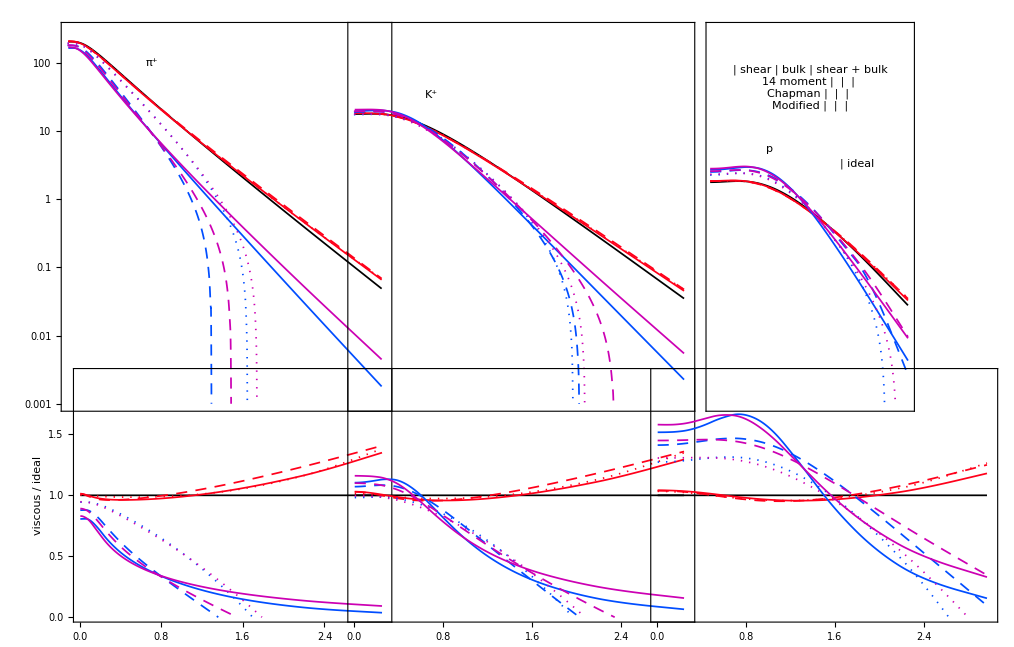
-Graphics-p_T (GeV)

```mathematica
SetDirectory@NotebookDirectory[];

pion = {idealπ,shear14π,shearCEπ,shearmodπ,bulk14π,bulkCEπ,bulkmodπ,shearbulk14π,shearbulkCEπ,shearbulkmodπ};
kaon= {idealK,shear14K,shearCEK,shearmodK,bulk14K,bulkCEK,bulkmodK,shearbulk14K,shearbulkCEK,shearbulkmodK};
proton={idealp,shear14p,shearCEp,shearmodp,bulk14p,bulkCEp,bulkmodp,shearbulk14p,shearbulkCEp,shearbulkmodp};

ratiopion = {ratioidealπ,ratioshear14π,ratioshearCEπ,ratioshearmodπ,ratiobulk14π,ratiobulkCEπ,ratiobulkmodπ,ratioshearbulk14π,ratioshearbulkCEπ,ratioshearbulkmodπ};
ratiokaon= {ratioidealK,ratioshear14K,ratioshearCEK,ratioshearmodK,ratiobulk14K,ratiobulkCEK,ratiobulkmodK,ratioshearbulk14K,ratioshearbulkCEK,ratioshearbulkmodK};
ratioproton={ratioidealp,ratioshear14p,ratioshearCEp,ratioshearmodp,ratiobulk14p,ratiobulkCEp,ratiobulkmodp, ratioshearbulk14p,ratioshearbulkCEp,ratioshearbulkmodp};

spectra=Panel[GraphicsGrid[{{

ListLogPlot[pion,PlotRange->{{0.0,3},{1.*10^-3,300}},Frame->True,FrameStyle->Black,FrameLabel->{"",""},FrameTicks->{{dNticks,dNticksnone},{pTticksnone,All}},BaseStyle->{FontSize->14},Joined->True,InterpolationOrder->2,ImageSize->450,AspectRatio->1.15,PlotStyle->style,Epilog->{Inset[legendπ,{0.8,4.6}]}, ImagePadding->{{a,b},{Automatic,Automatic}}],

ListLogPlot[kaon,PlotRange->{{0.005,3.0},{1.*10^-3,300}},Frame->True,FrameStyle->Black,FrameLabel->{"",""},FrameTicks->{{dNticksnone,dNticksnone},{pTticksnone,All}},Joined->True,BaseStyle->{FontSize->14},InterpolationOrder->2,ImageSize->450,AspectRatio->1.15,PlotStyle->style,Epilog->{Inset[legendK,{0.7,3.5}]},ImagePadding->{{a,b},{Automatic,Automatic}}],

ListLogPlot[proton,PlotRange->{{0.005,3.0},{1.*10^-3,300}},Frame->True,FrameStyle->Black,FrameLabel->{"",""},FrameTicks->{{dNticksnone,dNticks},{pTticksnone,All}},BaseStyle->{FontSize->14},Joined->True,InterpolationOrder->2,ImageSize->450,AspectRatio->1.15,PlotStyle->style,Epilog->{Inset[legendp,{0.9,1.7}],Inset[legenddf,{1.5,3.75}],Inset[legendideal,{2.2,1.2}]},ImagePadding->{{a,b},{Automatic,Automatic}}]},

{ListPlot[ratiopion,PlotRange->{{0.0,3},{0,2}},Frame->True,FrameStyle->Black,FrameLabel->{"",Style["viscous / ideal",FontSize->18,FontFamily->"Arial",Black]},FrameTicks->{{ratioticks,ratioticksnone},{Automatic,pTticksnone}},BaseStyle->{FontSize->14},Joined->True,InterpolationOrder->2,ImageSize->450,AspectRatio->0.75,PlotStyle->style, ImagePadding->{{a,b},{Automatic,Automatic}}],

ListPlot[ratiokaon,PlotRange->{{0.005,3.0},{0,2}},Frame->True,FrameStyle->Black,FrameLabel->{"",""},FrameTicks->{{ratioticksnone,ratioticksnone},{True,pTticksnone}},Joined->True,BaseStyle->{FontSize->14},InterpolationOrder->2,ImageSize->450,AspectRatio->0.75,PlotStyle->style,ImagePadding->{{a,b},{Automatic,Automatic}}],

ListPlot[ratioproton,PlotRange->{{0.005,3.0},{0,2}},Frame->True,FrameStyle->Black,FrameLabel->{"",""},FrameTicks->{{ratioticksnone,ratioticks},{True,pTticksnone}},BaseStyle->{FontSize->14},Joined->True,InterpolationOrder->2,ImageSize->450,AspectRatio->0.75,PlotStyle->style,ImagePadding->{{a,b},{Automatic,Automatic}}]}


},Spacings->{-116,-200},PlotLabel->Style["(dN/(2  π SubscriptBox[p, T] SubscriptBox[dp, T] dy))_(|_(y = 0))",FontSize->26,FontFamily->"Arial",Black]],{Style["p_T (GeV)",FontFamily->"Arial",FontSize->18]},{{Bottom,Center}},Appearance->"Frameless",FrameMargins->0,Background->White]

Export["modified_spectra2_500MeV.pdf",spectra];
```

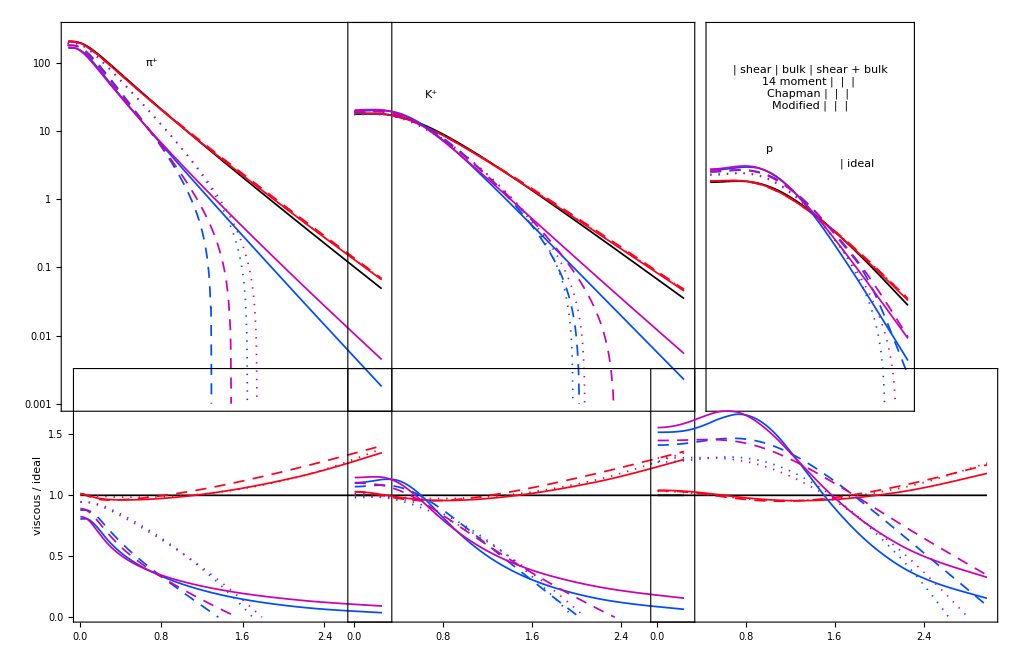
```mathematica
-Graphics-"\!\(\*SubscriptBox[\(p\), \(T\)]\) (GeV)"
```

-Graphics-p_T (GeV)